```mathematica
part1=Import[NotebookDirectory[]<>"part1.csv"];
(* Remove tail end columns that have no prices *)
data1=Select[part1,FreeQ[#,_Missing]&];
(* Remove first column because extra time is redundant *)
data1=data1[[All,2;;]];
(* Convert timestamps (column 1) into Mathematica-friendly date object *)
Timestamp[ts_]:=DateObject[{1970,1,1,0,0,0},TimeZone->"UTC"]+Quantity[ts,"Seconds"];
data1=MapAt[Timestamp[#]&,Rest[data1],{All,1}];
(* Grab head *)
head1=Rest[part1[[1]]];
(* Convert whole thing into Mathematica dataset *)
ds1=Dataset[AssociationThread[head1,#]&/@data1];

part2=Import[NotebookDirectory[]<>"part2.csv"];
data2=Select[part2,FreeQ[#,_Missing]&];
data2=data2[[All,2;;]];
data2=MapAt[Timestamp[#]&,Rest[data2],{All,1}];
head2=Rest[part2[[1]]];
ds2=Dataset[AssociationThread[head2,#]&/@data2];

part3=Import[NotebookDirectory[]<>"part3.csv"];
data3=Select[part3,FreeQ[#,_Missing]&];
data3=data3[[All,2;;]];
data3=MapAt[Timestamp[#]&,Rest[data3],{All,1}];
head3=Rest[part3[[1]]];
ds3=Dataset[AssociationThread[head3,#]&/@data3];

ds=DeleteDuplicates@Join[ds1,ds2,ds3];

ds=ds[All,{"Timestamp (UTC)","Len Sassaman","Hal Finney","Adam Back","Nick Szabo","David Kleiman","Other/Multiple "}]
```

Dataset[<>]

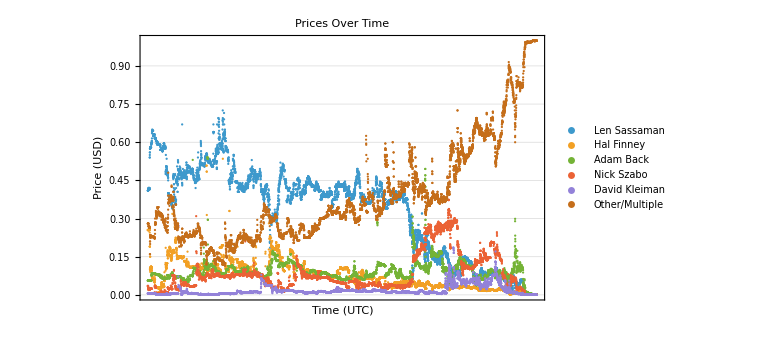

/Users/jeremyclark/Documents/Academia/Deliverables/Publications/01 Drafts/2024-PredictionMarkets/2024 HBO Money Electric/Data/graph.png

```mathematica
(* Plot *)

priceColumns=Keys[ds[[1]]]~DeleteCases~"Timestamp (UTC)"//Normal;
seriesList=Table[Normal[ds[[All,{"Timestamp (UTC)",col}]]][[All]]//Values,{col,priceColumns}];
DateListPlot[seriesList,PlotLegends->priceColumns,Joined->False,Frame->True,PlotTheme->"Detailed",PlotLabel->"Prices Over Time",PlotRange->All,ImageSize->Large,AxesLabel->{"Time (UTC)","Price (USD)"},DateTicksFormat->{"MonthNameShort"," ","DayShort"," ","Hour",":","Minute"}]

Export[NotebookDirectory[]<>"graph.png",%]
```

## Price Movements

```mathematica
threshold=0.02;        (*2% change*)
lookahead=Quantity[30,"Minutes"];  (*How far to look ahead for persistence*)

timeSeries=ds[All,{"Timestamp (UTC)","Len Sassaman"}]
times=timeSeries[All,"Timestamp (UTC)"]
prices=Normal[timeSeries[All,"Len Sassaman"]]


returns=Differences[Log[prices]]

jumpIndices=Select[Range[Length[returns]],Abs[returns[[#]]]>threshold&]
```

Dataset[<>]

Dataset[<>]

{0.41,0.41,0.41,0.41,0.41,0.41,0.41,0.415,0.415,0.415,0.415,0.415,0.415,0.415,0.415,0.42,0.42,0.42,0.42,0.42,0.42,0.42,0.42,0.415,0.415,0.415,0.415,0.415,0.42,0.42,0.42,0.42,0.415,0.415,0.415,0.54,0.54,0.55,0.56,0.56,0.575,0.575,0.575,0.575,0.575,0.575,0.58,0.58,0.58,0.58,0.58,0.58,0.58,0.58,0.58,0.58,0.58,0.58,0.58,0.58,0.58,0.58,0.59,0.59,0.595,0.595,0.595,0.595,0.595,0.595,0.595,0.595,0.6,0.6,0.605,0.605,0.6,0.615,0.635,0.64,0.645,0.645,0.645,0.65,0.645,0.645,0.645,0.645,0.645,0.645,0.645,0.645,0.645,0.645,0.645,0.645,0.645,0.645,0.645,0.625,0.625,0.625,0.625,0.625,0.625,0.625,0.625,0.625,0.625,0.625,0.63,0.63,0.63,0.63,0.63,0.63,0.63,0.63,0.63,0.63,0.63,0.63,0.63,0.63,0.63,0.63,0.63,0.63,0.62,0.62,0.615,0.615,0.615,0.615,0.615,0.615,0.615,0.615,0.615,0.615,0.615,0.615,0.615,0.615,0.615,0.615,0.615,0.615,0.615,0.615,0.615,0.61,0.605,0.605,0.605,0.605,0.605,0.605,0.605,0.605,0.605,0.605,0.605,0.605,0.605,0.605,0.6,0.595,0.595,0.595,0.595,0.6,0.6,0.6,0.6,0.6,0.6,0.6,0.6,0.6,0.6,0.6,0.59,0.59,0.59,0.59,0.59,0.59,0.59,0.59,0.59,0.59,0.59,0.59,0.59,0.595,0.59,0.59,0.59,0.59,0.59,0.59,0.59,0.59,0.59,0.59,0.59,0.59,0.59,0.59,0.59,0.59,0.59,0.59,0.59,0.59,0.59,0.59,0.59,0.59,0.59,0.59,0.59,0.59,0.59,0.59,0.59,0.59,0.59,0.59,0.59,0.585,0.59,0.585,0.58,0.57,0.57,0.57,0.57,0.57,0.57,0.57,0.57,0.57,0.57,0.57,0.57,0.57,0.57,0.575,0.575,0.575,0.57,0.575,0.575,0.575,0.575,0.575,0.57,0.57,0.57,0.575,0.575,0.575,0.575,0.57,0.57,0.57,0.565,0.565,0.565,0.565,0.565,0.565,0.565,0.565,0.565,0.565,0.565,0.58,0.58,0.585,0.58,0.58,0.575,0.575,0.58,0.58,0.585,0.585,0.585,0.585,0.58,0.58,0.585,0.585,0.585,0.595,0.595,0.595,0.595,0.595,0.595,0.595,0.595,0.59,0.59,0.585,0.585,0.58,0.58,0.575,0.575,0.575,0.58,0.58,0.58,0.585,0.585,0.585,0.585,0.585,0.585,0.585,0.58,0.58,0.58,0.58,0.58,0.58,0.575,0.575,0.485,0.48,0.475,0.475,0.55,0.49,0.485,0.485,0.49,0.49,0.49,0.505,0.505,0.505,0.505,0.505,0.505,0.5,0.5,0.535,0.495,0.495,0.49,0.49,0.49,0.485,0.485,0.485,0.485,0.48,0.485,0.485,0.475,0.475,0.47,0.47,0.47,0.475,0.475,0.475,0.475,0.47,0.465,0.47,0.475,0.46,0.46,0.45,0.4,0.4,0.4,0.4,0.4,0.4,0.4,0.39,0.395,0.39,0.39,0.395,0.395,0.395,0.395,0.385,0.385,0.385,0.385,0.385,0.385,0.385,0.385,0.375,0.38,0.385,0.385,0.385,0.385,0.385,0.385,0.385,0.38,0.38,0.385,0.385,0.385,0.385,0.385,0.385,0.39,0.39,0.39,0.39,0.39,0.385,0.38,0.365,0.355,0.385,0.375,0.365,0.365,0.375,0.37,0.37,0.375,0.37,0.37,0.37,0.37,0.375,0.37,0.37,0.37,0.36,0.36,0.36,0.36,0.36,0.36,0.36,0.355,0.355,0.35,0.35,0.34,0.34,0.345,0.345,0.345,0.345,0.38,0.38,0.375,0.375,0.375,0.375,0.375,0.375,0.375,0.365,0.465,0.465,0.46,0.455,0.46,0.475,0.47,0.465,0.47,0.465,0.465,0.46,0.47,0.42,0.41,0.435,0.435,0.405,0.395,0.385,0.385,0.385,0.385,0.385,0.385,0.385,0.385,0.385,0.385,0.385,0.38,0.375,0.415,0.375,0.375,0.375,0.475,0.47,0.385,0.38,0.365,0.36,0.36,0.36,0.36,0.355,0.355,0.355,0.355,0.355,0.355,0.37,0.37,0.37,0.375,0.42,0.445,0.44,0.445,0.455,0.455,0.45,0.45,0.45,0.45,0.45,0.445,0.44,0.45,0.45,0.45,0.46,0.455,0.505,0.465,0.455,0.455,0.455,0.455,0.455,0.455,0.445,0.405,0.405,0.43,0.435,0.435,0.435,0.435,0.495,0.53,0.525,0.52,0.46,0.475,0.49,0.49,0.49,0.49,0.49,0.49,0.475,0.47,0.47,0.47,0.46,0.455,0.455,0.485,0.495,0.485,0.475,0.455,0.475,0.49,0.485,0.485,0.485,0.475,0.48,0.48,0.48,0.505,0.49,0.49,0.49,0.49,0.49,0.495,0.495,0.49,0.48,0.48,0.5,0.48,0.475,0.49,0.485,0.485,0.485,0.485,0.47,0.47,0.485,0.475,0.47,0.48,0.475,0.475,0.46,0.47,0.47,0.48,0.475,0.47,0.47,0.47,0.455,0.455,0.46,0.46,0.46,0.46,0.46,0.46,0.46,0.44,0.44,0.67,0.43,0.435,0.47,0.48,0.48,0.475,0.47,0.47,0.47,0.47,0.47,0.47,0.495,0.48,0.47,0.475,0.475,0.475,0.48,0.475,0.475,0.475,0.475,0.475,0.475,0.475,0.475,0.475,0.48,0.465,0.48,0.475,0.475,0.47,0.485,0.485,0.485,0.485,0.49,0.485,0.48,0.46,0.46,0.46,0.46,0.46,0.46,0.46,0.46,0.46,0.46,0.46,0.46,0.46,0.46,0.46,0.465,0.465,0.47,0.47,0.47,0.475,0.475,0.475,0.48,0.475,0.48,0.48,0.48,0.48,0.48,0.48,0.48,0.48,0.48,0.475,0.485,0.49,0.52,0.52,0.51,0.51,0.485,0.49,0.455,0.455,0.46,0.465,0.51,0.5,0.5,0.48,0.48,0.48,0.48,0.48,0.48,0.48,0.48,0.48,0.495,0.485,0.485,0.485,0.485,0.485,0.485,0.485,0.51,0.505,0.485,0.5,0.5,0.505,0.505,0.5,0.5,0.505,0.505,0.505,0.505,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.5,0.505,0.5,0.5,0.5,0.5,0.5,0.49,0.48,0.485,0.485,0.485,0.485,0.485,0.485,0.485,0.485,0.485,0.485,0.485,0.485,0.485,0.485,0.485,0.48,0.48,0.48,0.48,0.475,0.49,0.485,0.485,0.48,0.485,0.49,0.49,0.49,0.49,0.49,0.49,0.49,0.49,0.49,0.49,0.49,0.49,0.495,0.495,0.495,0.495,0.495,0.495,0.495,0.495,0.495,0.495,0.495,0.495,0.495,0.495,0.485,0.485,0.485,0.485,0.485,0.485,0.48,0.48,0.48,0.47,0.47,0.47,0.47,0.47,0.47,0.47,0.465,0.46,0.46,0.46,0.46,0.455,0.455,0.455,0.455,0.455,0.455,0.455,0.455,0.455,0.455,0.455,0.455,0.45,0.45,0.45,0.455,0.455,0.455,0.455,0.45,0.45,0.44,0.44,0.44,0.44,0.44,0.44,0.445,0.445,0.445,0.44,0.44,0.42,0.45,0.45,0.45,0.45,0.45,0.45,0.445,0.45,0.45,0.45,0.455,0.45,0.445,0.445,0.45,0.47,0.465,0.49,0.48,0.48,0.48,0.48,0.48,0.48,0.47,0.46,0.46,0.48,0.48,0.48,0.48,0.5,0.49,0.49,0.45,0.45,0.45,0.45,0.455,0.455,0.46,0.47,0.48,0.54,0.475,0.47,0.485,0.56,0.49,0.49,0.49,0.49,0.48,0.47,0.47,0.465,0.465,0.465,0.465,0.465,0.465,0.47,0.46,0.46,0.46,0.455,0.455,0.455,0.455,0.455,0.49,0.495,0.495,0.495,0.495,0.515,0.505,0.5,0.5,0.5,0.5,0.52,0.525,0.525,0.515,0.51,0.51,0.51,0.51,0.53,0.52,0.515,0.52,0.52,0.52,0.52,0.605,0.6,0.59,0.595,0.585,0.565,0.55,0.555,0.54,0.54,0.55,0.54,0.535,0.54,0.51,0.51,0.515,0.515,0.515,0.515,0.515,0.515,0.515,0.515,0.515,0.515,0.515,0.515,0.515,0.515,0.515,0.515,0.515,0.51,0.515,0.515,0.515,0.515,0.515,0.515,0.51,0.51,0.51,0.51,0.51,0.51,0.51,0.51,0.51,0.51,0.51,0.51,0.51,0.51,0.51,0.515,0.515,0.51,0.51,0.51,0.515,0.515,0.51,0.51,0.515,0.515,0.51,0.505,0.505,0.505,0.505,0.515,0.515,0.515,0.51,0.515,0.515,0.515,0.52,0.535,0.535,0.54,0.54,0.54,0.54,0.54,0.54,0.545,0.545,0.545,0.545,0.53,0.53,0.53,0.53,0.53,0.53,0.53,0.53,0.53,0.53,0.53,0.535,0.535,0.55,0.555,0.555,0.555,0.55,0.555,0.555,0.555,0.555,0.55,0.55,0.54,0.54,0.535,0.55,0.53,0.53,0.535,0.535,0.535,0.53,0.53,0.535,0.53,0.53,0.525,0.535,0.53,0.53,0.525,0.525,0.525,0.525,0.525,0.525,0.53,0.53,0.53,0.535,0.52,0.52,0.52,0.52,0.525,0.525,0.525,0.52,0.52,0.52,0.525,0.525,0.525,0.525,0.525,0.525,0.52,0.52,0.52,0.53,0.53,0.53,0.535,0.525,0.525,0.53,0.525,0.525,0.525,0.525,0.525,0.525,0.52,0.525,0.525,0.525,0.515,0.52,0.52,0.52,0.52,0.52,0.52,0.52,0.52,0.52,0.515,0.515,0.515,0.515,0.515,0.51,0.51,0.51,0.51,0.51,0.51,0.51,0.51,0.505,0.51,0.51,0.51,0.51,0.51,0.51,0.505,0.505,0.505,0.505,0.505,0.505,0.51,0.51,0.51,0.51,0.51,0.51,0.51,0.51,0.51,0.505,0.505,0.505,0.505,0.505,0.505,0.53,0.525,0.53,0.525,0.555,0.67,0.635,0.64,0.64,0.64,0.64,0.64,0.64,0.64,0.53,0.515,0.515,0.53,0.525,0.515,0.52,0.525,0.525,0.525,0.525,0.525,0.525,0.515,0.525,0.525,0.525,0.525,0.525,0.525,0.535,0.535,0.545,0.545,0.545,0.545,0.545,0.545,0.545,0.545,0.545,0.545,0.545,0.545,0.545,0.565,0.575,0.57,0.57,0.565,0.55,0.555,0.56,0.55,0.56,0.565,0.56,0.56,0.52,0.515,0.525,0.525,0.525,0.52,0.5,0.495,0.495,0.5,0.525,0.67,0.575,0.565,0.57,0.57,0.585,0.59,0.58,0.58,0.58,0.58,0.575,0.575,0.57,0.555,0.555,0.555,0.555,0.555,0.555,0.56,0.56,0.575,0.56,0.56,0.695,0.695,0.665,0.635,0.615,0.57,0.56,0.56,0.68,0.68,0.67,0.69,0.66,0.645,0.615,0.59,0.575,0.61,0.61,0.595,0.62,0.62,0.62,0.62,0.63,0.615,0.595,0.595,0.595,0.595,0.595,0.595,0.595,0.595,0.595,0.595,0.595,0.595,0.595,0.585,0.585,0.585,0.585,0.585,0.585,0.575,0.58,0.58,0.58,0.585,0.59,0.59,0.585,0.575,0.575,0.575,0.575,0.575,0.575,0.58,0.58,0.57,0.58,0.58,0.605,0.595,0.6,0.6,0.59,0.595,0.585,0.59,0.595,0.595,0.595,0.595,0.685,0.65,0.61,0.585,0.615,0.725,0.695,0.69,0.67,0.68,0.69,0.67,0.63,0.635,0.625,0.565,0.565,0.565,0.565,0.575,0.57,0.56,0.565,0.56,0.615,0.615,0.615,0.615,0.615,0.715,0.69,0.635,0.64,0.67,0.63,0.625,0.625,0.625,0.63,0.63,0.63,0.63,0.645,0.635,0.635,0.64,0.65,0.64,0.615,0.615,0.615,0.615,0.615,0.615,0.615,0.605,0.605,0.605,0.605,0.585,0.585,0.585,0.58,0.58,0.58,0.58,0.58,0.58,0.58,0.58,0.565,0.57,0.57,0.57,0.57,0.57,0.57,0.57,0.57,0.57,0.57,0.58,0.57,0.57,0.57,0.565,0.565,0.565,0.565,0.565,0.565,0.565,0.565,0.565,0.57,0.57,0.57,0.57,0.57,0.565,0.565,0.565,0.565,0.565,0.56,0.535,0.535,0.535,0.515,0.53,0.53,0.525,0.525,0.53,0.53,0.54,0.54,0.45,0.445,0.45,0.45,0.45,0.44,0.44,0.44,0.44,0.44,0.445,0.445,0.435,0.435,0.455,0.44,0.445,0.445,0.44,0.435,0.45,0.425,0.415,0.415,0.455,0.45,0.44,0.45,0.46,0.46,0.46,0.46,0.46,0.46,0.46,0.475,0.475,0.475,0.475,0.475,0.475,0.47,0.47,0.47,0.47,0.47,0.49,0.475,0.48,0.48,0.48,0.48,0.48,0.48,0.46,0.44,0.44,0.455,0.47,0.46,0.455,0.47,0.445,0.445,0.445,0.465,0.465,0.465,0.465,0.47,0.47,0.47,0.465,0.455,0.47,0.47,0.48,0.505,0.535,0.53,0.53,0.53,0.53,0.53,0.505,0.495,0.495,0.53,0.495,0.495,0.495,0.55,0.55,0.545,0.55,0.525,0.525,0.525,0.525,0.515,0.52,0.51,0.51,0.505,0.505,0.495,0.495,0.495,0.495,0.495,0.49,0.495,0.485,0.485,0.485,0.485,0.49,0.495,0.495,0.485,0.485,0.485,0.48,0.48,0.48,0.445,0.445,0.445,0.445,0.445,0.445,0.445,0.445,0.445,0.445,0.445,0.445,0.445,0.445,0.445,0.445,0.445,0.445,0.44,0.44,0.44,0.445,0.445,0.445,0.445,0.445,0.445,0.445,0.445,0.445,0.445,0.445,0.44,0.44,0.44,0.44,0.44,0.44,0.44,0.44,0.42,0.42,0.42,0.42,0.425,0.405,0.405,0.405,0.405,0.405,0.405,0.405,0.405,0.405,0.405,0.405,0.405,0.405,0.405,0.405,0.405,0.42,0.415,0.425,0.435,0.435,0.435,0.435,0.435,0.435,0.435,0.43,0.43,0.43,0.435,0.435,0.435,0.435,0.435,0.435,0.435,0.435,0.435,0.435,0.435,0.435,0.44,0.42,0.425,0.425,0.425,0.425,0.43,0.425,0.415,0.415,0.425,0.425,0.425,0.435,0.435,0.435,0.435,0.435,0.435,0.435,0.435,0.435,0.435,0.435,0.435,0.435,0.435,0.425,0.425,0.415,0.415,0.415,0.415,0.415,0.415,0.415,0.415,0.415,0.41,0.415,0.41,0.41,0.41,0.41,0.43,0.44,0.425,0.425,0.425,0.43,0.425,0.425,0.425,0.425,0.425,0.425,0.42,0.42,0.42,0.42,0.42,0.42,0.415,0.41,0.41,0.41,0.405,0.405,0.405,0.405,0.405,0.41,0.41,0.405,0.405,0.405,0.405,0.405,0.405,0.405,0.425,0.42,0.42,0.42,0.42,0.42,0.42,0.42,0.42,0.42,0.42,0.425,0.425,0.425,0.425,0.425,0.425,0.435,0.425,0.415,0.415,0.415,0.415,0.415,0.415,0.42,0.42,0.42,0.42,0.42,0.42,0.42,0.44,0.435,0.435,0.435,0.435,0.435,0.435,0.425,0.425,0.425,0.425,0.425,0.425,0.425,0.425,0.43,0.43,0.43,0.43,0.43,0.43,0.43,0.43,0.43,0.425,0.425,0.42,0.45,0.43,0.435,0.42,0.42,0.42,0.43,0.425,0.455,0.425,0.44,0.435,0.465,0.45,0.445,0.435,0.47,0.455,0.455,0.455,0.455,0.455,0.46,0.46,0.46,0.465,0.455,0.455,0.455,0.455,0.45,0.445,0.445,0.46,0.46,0.455,0.455,0.455,0.455,0.455,0.45,0.45,0.45,0.45,0.45,0.47,0.46,0.45,0.45,0.45,0.45,0.45,0.495,0.465,0.465,0.465,0.465,0.465,0.455,0.475,0.475,0.49,0.475,0.475,0.475,0.47,0.47,0.475,0.475,0.475,0.475,0.475,0.475,0.475,0.485,0.475,0.465,0.5,0.485,0.53,0.485,0.485,0.485,0.475,0.48,0.475,0.485,0.48,0.505,0.495,0.49,0.485,0.485,0.485,0.49,0.495,0.495,0.49,0.49,0.49,0.49,0.49,0.485,0.49,0.49,0.49,0.475,0.455,0.455,0.45,0.43,0.42,0.425,0.43,0.465,0.465,0.46,0.445,0.455,0.475,0.475,0.475,0.475,0.475,0.475,0.475,0.47,0.47,0.47,0.47,0.47,0.465,0.465,0.475,0.475,0.475,0.49,0.49,0.49,0.485,0.485,0.485,0.485,0.485,0.48,0.475,0.475,0.475,0.475,0.475,0.475,0.475,0.455,0.445,0.445,0.47,0.46,0.475,0.455,0.45,0.45,0.455,0.44,0.445,0.445,0.465,0.46,0.465,0.465,0.465,0.465,0.465,0.47,0.47,0.47,0.47,0.475,0.475,0.475,0.47,0.465,0.465,0.47,0.455,0.455,0.455,0.455,0.455,0.455,0.465,0.47,0.47,0.47,0.47,0.47,0.47,0.465,0.465,0.465,0.465,0.465,0.465,0.475,0.47,0.475,0.475,0.475,0.475,0.475,0.475,0.475,0.475,0.475,0.475,0.475,0.475,0.475,0.475,0.475,0.475,0.475,0.475,0.475,0.47,0.47,0.47,0.47,0.485,0.485,0.485,0.485,0.495,0.475,0.475,0.485,0.485,0.48,0.48,0.48,0.48,0.475,0.455,0.465,0.47,0.465,0.455,0.47,0.465,0.435,0.43,0.43,0.435,0.425,0.415,0.415,0.405,0.405,0.405,0.405,0.405,0.405,0.405,0.405,0.415,0.41,0.41,0.41,0.41,0.41,0.41,0.41,0.415,0.415,0.415,0.415,0.415,0.415,0.395,0.395,0.395,0.405,0.405,0.405,0.405,0.405,0.405,0.405,0.405,0.395,0.415,0.415,0.405,0.4,0.41,0.395,0.395,0.395,0.375,0.38,0.39,0.385,0.385,0.385,0.375,0.375,0.375,0.375,0.375,0.375,0.375,0.365,0.375,0.375,0.38,0.38,0.395,0.405,0.395,0.395,0.4,0.405,0.4,0.41,0.405,0.41,0.415,0.425,0.415,0.42,0.42,0.425,0.415,0.43,0.415,0.41,0.42,0.415,0.425,0.425,0.43,0.425,0.415,0.41,0.41,0.41,0.415,0.415,0.415,0.415,0.415,0.425,0.43,0.43,0.43,0.43,0.435,0.435,0.425,0.425,0.425,0.425,0.425,0.425,0.435,0.43,0.43,0.43,0.395,0.395,0.395,0.395,0.395,0.4,0.395,0.385,0.385,0.385,0.385,0.385,0.385,0.385,0.385,0.4,0.37,0.375,0.395,0.375,0.31,0.33,0.34,0.365,0.355,0.35,0.415,0.395,0.39,0.395,0.41,0.375,0.375,0.37,0.38,0.385,0.385,0.375,0.375,0.375,0.375,0.355,0.335,0.335,0.335,0.355,0.335,0.315,0.21,0.205,0.205,0.255,0.185,0.205,0.235,0.235,0.21,0.225,0.225,0.225,0.225,0.305,0.31,0.305,0.3,0.295,0.3,0.3,0.285,0.285,0.29,0.29,0.29,0.285,0.285,0.285,0.285,0.28,0.275,0.275,0.285,0.305,0.305,0.305,0.295,0.295,0.295,0.295,0.305,0.305,0.305,0.305,0.305,0.31,0.31,0.31,0.3,0.3,0.31,0.32,0.31,0.305,0.31,0.295,0.295,0.295,0.31,0.3,0.3,0.3,0.3,0.295,0.295,0.295,0.295,0.3,0.3,0.3,0.3,0.3,0.3,0.305,0.305,0.305,0.305,0.305,0.305,0.305,0.31,0.315,0.295,0.315,0.3,0.295,0.295,0.295,0.3,0.305,0.315,0.315,0.32,0.335,0.32,0.305,0.295,0.305,0.325,0.31,0.3,0.3,0.3,0.3,0.3,0.3,0.3,0.3,0.295,0.3,0.305,0.305,0.305,0.305,0.305,0.305,0.295,0.295,0.305,0.305,0.3,0.3,0.32,0.31,0.3,0.29,0.285,0.285,0.285,0.31,0.305,0.305,0.305,0.295,0.295,0.3,0.3,0.325,0.325,0.32,0.32,0.315,0.315,0.335,0.335,0.335,0.335,0.34,0.34,0.345,0.345,0.355,0.355,0.355,0.355,0.38,0.37,0.37,0.37,0.39,0.39,0.41,0.415,0.405,0.42,0.42,0.43,0.415,0.41,0.41,0.435,0.435,0.36,0.37,0.375,0.355,0.405,0.425,0.45,0.435,0.435,0.435,0.46,0.445,0.44,0.445,0.44,0.44,0.44,0.435,0.435,0.45,0.465,0.47,0.465,0.45,0.455,0.455,0.52,0.5,0.49,0.485,0.475,0.47,0.47,0.47,0.475,0.46,0.465,0.465,0.465,0.475,0.48,0.48,0.48,0.46,0.49,0.485,0.5,0.495,0.495,0.49,0.475,0.47,0.485,0.475,0.485,0.485,0.475,0.48,0.475,0.475,0.495,0.495,0.495,0.495,0.5,0.5,0.505,0.505,0.5,0.495,0.515,0.515,0.515,0.51,0.51,0.51,0.51,0.51,0.505,0.505,0.505,0.5,0.5,0.505,0.51,0.51,0.465,0.49,0.495,0.49,0.49,0.49,0.49,0.49,0.49,0.49,0.49,0.49,0.49,0.49,0.49,0.49,0.49,0.49,0.485,0.455,0.455,0.455,0.455,0.455,0.455,0.455,0.455,0.455,0.455,0.455,0.45,0.435,0.44,0.45,0.445,0.445,0.45,0.455,0.455,0.445,0.44,0.45,0.45,0.44,0.44,0.44,0.44,0.43,0.425,0.42,0.42,0.42,0.42,0.42,0.42,0.425,0.425,0.37,0.37,0.37,0.37,0.365,0.365,0.365,0.365,0.37,0.365,0.37,0.37,0.37,0.375,0.375,0.375,0.375,0.375,0.375,0.375,0.375,0.39,0.385,0.385,0.42,0.41,0.415,0.415,0.415,0.415,0.415,0.415,0.39,0.41,0.41,0.41,0.41,0.41,0.41,0.41,0.41,0.415,0.42,0.415,0.41,0.42,0.42,0.42,0.42,0.42,0.42,0.42,0.42,0.42,0.42,0.42,0.42,0.42,0.42,0.36,0.365,0.375,0.375,0.37,0.37,0.37,0.37,0.365,0.365,0.365,0.385,0.375,0.36,0.36,0.36,0.36,0.36,0.36,0.39,0.4,0.4,0.4,0.405,0.39,0.385,0.385,0.38,0.38,0.38,0.385,0.385,0.385,0.38,0.375,0.375,0.375,0.375,0.385,0.385,0.385,0.385,0.385,0.385,0.385,0.385,0.38,0.38,0.38,0.38,0.39,0.395,0.395,0.395,0.395,0.395,0.395,0.395,0.395,0.395,0.395,0.405,0.405,0.405,0.405,0.415,0.415,0.415,0.435,0.43,0.425,0.395,0.395,0.435,0.44,0.44,0.435,0.435,0.435,0.435,0.435,0.435,0.435,0.435,0.435,0.435,0.435,0.435,0.435,0.435,0.435,0.435,0.435,0.435,0.435,0.435,0.435,0.435,0.435,0.435,0.435,0.435,0.435,0.435,0.435,0.435,0.435,0.435,0.43,0.435,0.415,0.415,0.415,0.395,0.395,0.395,0.395,0.395,0.395,0.395,0.395,0.395,0.395,0.395,0.395,0.39,0.39,0.39,0.39,0.39,0.39,0.39,0.39,0.39,0.39,0.39,0.39,0.39,0.4,0.405,0.415,0.415,0.455,0.45,0.455,0.45,0.45,0.455,0.455,0.455,0.455,0.455,0.455,0.455,0.455,0.455,0.46,0.46,0.455,0.42,0.425,0.415,0.42,0.435,0.435,0.435,0.435,0.43,0.435,0.435,0.425,0.425,0.445,0.445,0.445,0.445,0.43,0.43,0.435,0.43,0.445,0.445,0.45,0.445,0.45,0.445,0.445,0.4,0.4,0.4,0.42,0.405,0.4,0.395,0.395,0.395,0.395,0.38,0.39,0.395,0.395,0.395,0.395,0.395,0.395,0.395,0.395,0.375,0.375,0.375,0.375,0.375,0.375,0.375,0.385,0.385,0.385,0.385,0.385,0.385,0.385,0.375,0.395,0.395,0.395,0.395,0.395,0.395,0.4,0.4,0.4,0.395,0.395,0.405,0.405,0.405,0.405,0.405,0.41,0.415,0.41,0.405,0.405,0.405,0.405,0.405,0.415,0.415,0.41,0.41,0.41,0.41,0.41,0.41,0.41,0.41,0.41,0.405,0.405,0.405,0.405,0.425,0.43,0.43,0.425,0.425,0.425,0.425,0.405,0.405,0.4,0.395,0.405,0.405,0.4,0.4,0.4,0.4,0.4,0.4,0.4,0.4,0.4,0.4,0.4,0.4,0.4,0.4,0.4,0.4,0.4,0.4,0.405,0.41,0.41,0.41,0.42,0.425,0.425,0.43,0.435,0.445,0.44,0.44,0.44,0.44,0.44,0.44,0.445,0.44,0.44,0.44,0.44,0.44,0.44,0.44,0.44,0.44,0.44,0.44,0.44,0.44,0.44,0.435,0.435,0.435,0.435,0.435,0.435,0.435,0.455,0.455,0.46,0.46,0.46,0.46,0.46,0.46,0.46,0.46,0.46,0.465,0.465,0.465,0.465,0.465,0.455,0.455,0.455,0.455,0.455,0.455,0.455,0.455,0.455,0.455,0.45,0.455,0.46,0.455,0.46,0.455,0.455,0.455,0.455,0.455,0.45,0.445,0.445,0.445,0.445,0.44,0.445,0.445,0.44,0.44,0.44,0.44,0.445,0.435,0.435,0.435,0.435,0.435,0.435,0.445,0.44,0.44,0.44,0.435,0.435,0.435,0.435,0.435,0.435,0.435,0.435,0.435,0.435,0.435,0.435,0.435,0.435,0.435,0.435,0.435,0.435,0.435,0.425,0.425,0.435,0.435,0.435,0.43,0.43,0.43,0.43,0.43,0.43,0.43,0.43,0.425,0.425,0.425,0.425,0.425,0.425,0.425,0.425,0.425,0.425,0.425,0.425,0.425,0.425,0.425,0.43,0.43,0.43,0.425,0.425,0.425,0.425,0.425,0.425,0.425,0.425,0.425,0.425,0.425,0.425,0.425,0.425,0.425,0.425,0.425,0.425,0.425,0.425,0.425,0.425,0.425,0.415,0.415,0.41,0.41,0.41,0.41,0.41,0.41,0.41,0.415,0.415,0.415,0.42,0.42,0.42,0.42,0.42,0.425,0.425,0.415,0.415,0.42,0.42,0.42,0.435,0.435,0.44,0.44,0.44,0.44,0.44,0.435,0.445,0.435,0.435,0.435,0.435,0.43,0.425,0.425,0.43,0.43,0.43,0.43,0.435,0.435,0.435,0.435,0.435,0.435,0.435,0.425,0.425,0.425,0.43,0.43,0.43,0.43,0.425,0.425,0.435,0.43,0.43,0.43,0.425,0.42,0.415,0.42,0.42,0.42,0.42,0.425,0.425,0.415,0.415,0.41,0.41,0.41,0.41,0.41,0.41,0.41,0.405,0.405,0.405,0.405,0.41,0.41,0.41,0.41,0.41,0.41,0.41,0.41,0.41,0.41,0.41,0.41,0.41,0.41,0.41,0.41,0.41,0.41,0.41,0.41,0.41,0.41,0.41,0.41,0.41,0.41,0.41,0.375,0.375,0.375,0.375,0.375,0.39,0.38,0.39,0.38,0.39,0.385,0.385,0.385,0.385,0.385,0.385,0.385,0.385,0.385,0.385,0.375,0.38,0.39,0.39,0.39,0.395,0.395,0.395,0.395,0.395,0.395,0.395,0.395,0.395,0.395,0.395,0.395,0.395,0.395,0.395,0.395,0.395,0.4,0.4,0.4,0.4,0.4,0.405,0.405,0.405,0.395,0.395,0.395,0.395,0.395,0.385,0.385,0.4,0.395,0.395,0.395,0.395,0.395,0.395,0.395,0.395,0.395,0.395,0.395,0.395,0.395,0.395,0.395,0.395,0.395,0.395,0.395,0.395,0.395,0.395,0.395,0.395,0.395,0.395,0.395,0.395,0.395,0.395,0.395,0.395,0.395,0.395,0.395,0.395,0.385,0.385,0.385,0.385,0.385,0.385,0.39,0.39,0.39,0.39,0.39,0.39,0.39,0.39,0.39,0.39,0.39,0.39,0.39,0.395,0.395,0.395,0.4,0.405,0.395,0.395,0.39,0.39,0.39,0.39,0.39,0.39,0.385,0.385,0.385,0.385,0.385,0.385,0.385,0.385,0.385,0.385,0.385,0.385,0.385,0.385,0.385,0.385,0.385,0.385,0.385,0.385,0.385,0.385,0.385,0.385,0.385,0.385,0.385,0.385,0.39,0.39,0.39,0.39,0.39,0.395,0.39,0.395,0.395,0.395,0.39,0.42,0.4,0.405,0.405,0.405,0.41,0.405,0.405,0.405,0.405,0.405,0.405,0.405,0.405,0.405,0.405,0.405,0.405,0.405,0.405,0.405,0.395,0.405,0.395,0.405,0.4,0.4,0.395,0.395,0.405,0.405,0.405,0.405,0.405,0.405,0.4,0.395,0.395,0.395,0.395,0.395,0.395,0.395,0.395,0.395,0.365,0.37,0.37,0.36,0.345,0.345,0.345,0.345,0.345,0.345,0.345,0.345,0.355,0.355,0.355,0.355,0.355,0.355,0.355,0.355,0.355,0.355,0.355,0.355,0.375,0.375,0.375,0.375,0.375,0.375,0.375,0.375,0.375,0.375,0.375,0.375,0.375,0.375,0.375,0.375,0.375,0.375,0.375,0.375,0.375,0.375,0.375,0.375,0.375,0.375,0.375,0.375,0.385,0.385,0.385,0.395,0.405,0.405,0.405,0.405,0.405,0.405,0.425,0.425,0.425,0.425,0.425,0.425,0.425,0.425,0.425,0.425,0.425,0.425,0.425,0.43,0.43,0.43,0.43,0.43,0.43,0.43,0.435,0.43,0.42,0.42,0.415,0.415,0.415,0.415,0.415,0.415,0.385,0.375,0.395,0.395,0.395,0.39,0.39,0.39,0.39,0.39,0.39,0.39,0.39,0.39,0.39,0.39,0.39,0.39,0.385,0.385,0.395,0.395,0.4,0.395,0.395,0.395,0.405,0.425,0.44,0.435,0.445,0.44,0.435,0.43,0.43,0.425,0.425,0.43,0.435,0.435,0.43,0.43,0.43,0.43,0.43,0.43,0.43,0.43,0.43,0.43,0.425,0.425,0.43,0.435,0.435,0.435,0.435,0.435,0.435,0.435,0.435,0.435,0.435,0.435,0.435,0.435,0.435,0.435,0.435,0.435,0.435,0.435,0.435,0.435,0.435,0.435,0.435,0.435,0.435,0.435,0.425,0.425,0.425,0.425,0.425,0.425,0.425,0.425,0.425,0.425,0.425,0.425,0.425,0.425,0.425,0.425,0.425,0.425,0.425,0.425,0.425,0.425,0.425,0.425,0.43,0.435,0.435,0.43,0.43,0.43,0.43,0.43,0.43,0.43,0.43,0.43,0.43,0.43,0.43,0.43,0.43,0.43,0.43,0.425,0.425,0.43,0.43,0.43,0.43,0.43,0.43,0.43,0.43,0.44,0.415,0.415,0.415,0.415,0.41,0.41,0.41,0.41,0.41,0.415,0.42,0.42,0.42,0.42,0.42,0.425,0.445,0.435,0.435,0.435,0.425,0.42,0.42,0.42,0.42,0.425,0.425,0.425,0.425,0.425,0.425,0.42,0.415,0.415,0.415,0.415,0.385,0.395,0.395,0.395,0.395,0.395,0.39,0.39,0.39,0.39,0.39,0.39,0.39,0.39,0.395,0.395,0.39,0.39,0.39,0.39,0.395,0.4,0.395,0.4,0.39,0.39,0.39,0.39,0.395,0.41,0.41,0.405,0.4,0.395,0.395,0.395,0.395,0.395,0.405,0.405,0.395,0.39,0.395,0.4,0.4,0.405,0.415,0.42,0.425,0.425,0.415,0.415,0.42,0.42,0.42,0.425,0.425,0.425,0.395,0.395,0.4,0.4,0.4,0.4,0.4,0.405,0.405,0.405,0.4,0.395,0.405,0.405,0.405,0.395,0.39,0.375,0.375,0.375,0.375,0.375,0.375,0.375,0.375,0.375,0.375,0.375,0.375,0.375,0.375,0.375,0.375,0.375,0.375,0.375,0.375,0.375,0.375,0.375,0.375,0.375,0.375,0.38,0.38,0.38,0.38,0.38,0.38,0.38,0.38,0.38,0.38,0.38,0.38,0.385,0.385,0.39,0.395,0.395,0.395,0.395,0.395,0.395,0.395,0.395,0.395,0.395,0.395,0.395,0.395,0.39,0.39,0.39,0.385,0.385,0.385,0.385,0.385,0.385,0.38,0.38,0.38,0.38,0.38,0.395,0.395,0.395,0.405,0.4,0.405,0.4,0.395,0.39,0.395,0.395,0.39,0.39,0.395,0.395,0.4,0.415,0.41,0.405,0.415,0.415,0.415,0.405,0.405,0.4,0.42,0.43,0.43,0.43,0.44,0.44,0.44,0.44,0.44,0.44,0.44,0.44,0.44,0.44,0.44,0.44,0.45,0.445,0.45,0.445,0.445,0.445,0.45,0.435,0.44,0.44,0.44,0.44,0.44,0.455,0.455,0.465,0.46,0.465,0.465,0.46,0.46,0.46,0.46,0.46,0.495,0.485,0.485,0.485,0.485,0.405,0.405,0.405,0.405,0.405,0.41,0.415,0.41,0.405,0.405,0.405,0.405,0.405,0.415,0.415,0.41,0.41,0.41,0.41,0.41,0.41,0.41,0.41,0.41,0.405,0.405,0.405,0.405,0.425,0.43,0.43,0.425,0.425,0.425,0.425,0.405,0.405,0.4,0.395,0.405,0.405,0.4,0.4,0.4,0.4,0.4,0.4,0.4,0.4,0.4,0.4,0.4,0.4,0.4,0.4,0.4,0.4,0.4,0.4,0.405,0.41,0.41,0.41,0.42,0.425,0.425,0.43,0.435,0.445,0.44,0.44,0.44,0.44,0.44,0.44,0.445,0.44,0.44,0.44,0.44,0.44,0.44,0.44,0.44,0.44,0.44,0.44,0.44,0.44,0.44,0.435,0.435,0.435,0.435,0.435,0.435,0.435,0.455,0.455,0.46,0.46,0.46,0.46,0.46,0.46,0.46,0.46,0.46,0.465,0.465,0.465,0.465,0.465,0.455,0.455,0.455,0.455,0.455,0.455,0.455,0.455,0.455,0.455,0.45,0.455,0.46,0.455,0.46,0.455,0.455,0.455,0.455,0.455,0.45,0.445,0.445,0.445,0.445,0.44,0.445,0.445,0.44,0.44,0.44,0.44,0.445,0.435,0.435,0.435,0.435,0.435,0.435,0.445,0.44,0.44,0.44,0.435,0.435,0.435,0.435,0.435,0.435,0.435,0.435,0.435,0.435,0.435,0.435,0.435,0.435,0.435,0.435,0.435,0.435,0.435,0.425,0.425,0.435,0.435,0.435,0.43,0.43,0.43,0.43,0.43,0.43,0.43,0.43,0.425,0.425,0.425,0.425,0.425,0.425,0.425,0.425,0.425,0.425,0.425,0.425,0.425,0.425,0.425,0.43,0.43,0.43,0.425,0.425,0.425,0.425,0.425,0.425,0.425,0.425,0.425,0.425,0.425,0.425,0.425,0.425,0.425,0.425,0.425,0.425,0.425,0.425,0.425,0.425,0.425,0.415,0.415,0.41,0.41,0.41,0.41,0.41,0.41,0.41,0.415,0.415,0.415,0.42,0.42,0.42,0.42,0.42,0.425,0.425,0.415,0.415,0.42,0.42,0.42,0.435,0.435,0.44,0.44,0.44,0.44,0.44,0.435,0.445,0.435,0.435,0.435,0.435,0.43,0.425,0.425,0.43,0.43,0.43,0.43,0.435,0.435,0.435,0.435,0.435,0.435,0.435,0.425,0.425,0.425,0.43,0.43,0.43,0.43,0.425,0.425,0.435,0.43,0.43,0.43,0.425,0.42,0.415,0.42,0.42,0.42,0.42,0.425,0.425,0.415,0.415,0.41,0.41,0.41,0.41,0.41,0.41,0.41,0.405,0.405,0.405,0.405,0.41,0.41,0.41,0.41,0.41,0.41,0.41,0.41,0.41,0.41,0.41,0.41,0.41,0.41,0.41,0.41,0.41,0.41,0.41,0.41,0.41,0.41,0.41,0.41,0.41,0.41,0.41,0.375,0.375,0.375,0.375,0.375,0.39,0.38,0.39,0.38,0.39,0.385,0.385,0.385,0.385,0.385,0.385,0.385,0.385,0.385,0.385,0.375,0.38,0.39,0.39,0.39,0.395,0.395,0.395,0.395,0.395,0.395,0.395,0.395,0.395,0.395,0.395,0.395,0.395,0.395,0.395,0.395,0.395,0.4,0.4,0.4,0.4,0.4,0.405,0.405,0.405,0.395,0.395,0.395,0.395,0.395,0.385,0.385,0.4,0.395,0.395,0.395,0.395,0.395,0.395,0.395,0.395,0.395,0.395,0.395,0.395,0.395,0.395,0.395,0.395,0.395,0.395,0.395,0.395,0.395,0.395,0.395,0.395,0.395,0.395,0.395,0.395,0.395,0.395,0.395,0.395,0.395,0.395,0.395,0.395,0.385,0.385,0.385,0.385,0.385,0.385,0.39,0.39,0.39,0.39,0.39,0.39,0.39,0.39,0.39,0.39,0.39,0.39,0.39,0.395,0.395,0.395,0.4,0.405,0.395,0.395,0.39,0.39,0.39,0.39,0.39,0.39,0.385,0.385,0.385,0.385,0.385,0.385,0.385,0.385,0.385,0.385,0.385,0.385,0.385,0.385,0.385,0.385,0.385,0.385,0.385,0.385,0.385,0.385,0.385,0.385,0.385,0.385,0.385,0.385,0.39,0.39,0.39,0.39,0.39,0.395,0.39,0.395,0.395,0.395,0.39,0.42,0.4,0.405,0.405,0.405,0.41,0.405,0.405,0.405,0.405,0.405,0.405,0.405,0.405,0.405,0.405,0.405,0.405,0.405,0.405,0.405,0.395,0.405,0.395,0.405,0.4,0.4,0.395,0.395,0.405,0.405,0.405,0.405,0.405,0.405,0.4,0.395,0.395,0.395,0.395,0.395,0.395,0.395,0.395,0.395,0.365,0.37,0.37,0.36,0.345,0.345,0.345,0.345,0.345,0.345,0.345,0.345,0.355,0.355,0.355,0.355,0.355,0.355,0.355,0.355,0.355,0.355,0.355,0.355,0.375,0.375,0.375,0.375,0.375,0.375,0.375,0.375,0.375,0.375,0.375,0.375,0.375,0.375,0.375,0.375,0.375,0.375,0.375,0.375,0.375,0.375,0.375,0.375,0.375,0.375,0.375,0.375,0.385,0.385,0.385,0.395,0.405,0.405,0.405,0.405,0.405,0.405,0.425,0.425,0.425,0.425,0.425,0.425,0.425,0.425,0.425,0.425,0.425,0.425,0.425,0.43,0.43,0.43,0.43,0.43,0.43,0.43,0.435,0.43,0.42,0.42,0.415,0.415,0.415,0.415,0.415,0.415,0.385,0.375,0.395,0.395,0.395,0.39,0.39,0.39,0.39,0.39,0.39,0.39,0.39,0.39,0.39,0.39,0.39,0.39,0.385,0.385,0.395,0.395,0.4,0.395,0.395,0.395,0.405,0.425,0.44,0.435,0.445,0.44,0.435,0.43,0.43,0.425,0.425,0.43,0.435,0.435,0.43,0.43,0.43,0.43,0.43,0.43,0.43,0.43,0.43,0.43,0.425,0.425,0.43,0.435,0.435,0.435,0.435,0.435,0.435,0.435,0.435,0.435,0.435,0.435,0.435,0.435,0.435,0.435,0.435,0.435,0.435,0.435,0.435,0.435,0.435,0.435,0.435,0.435,0.435,0.435,0.425,0.425,0.425,0.425,0.425,0.425,0.425,0.425,0.425,0.425,0.425,0.425,0.425,0.425,0.425,0.425,0.425,0.425,0.425,0.425,0.425,0.425,0.425,0.425,0.43,0.435,0.435,0.43,0.43,0.43,0.43,0.43,0.43,0.43,0.43,0.43,0.43,0.43,0.43,0.43,0.43,0.43,0.43,0.425,0.425,0.43,0.43,0.43,0.43,0.43,0.43,0.43,0.43,0.44,0.415,0.415,0.415,0.415,0.41,0.41,0.41,0.41,0.41,0.415,0.42,0.42,0.42,0.42,0.42,0.425,0.445,0.435,0.435,0.435,0.425,0.42,0.42,0.42,0.42,0.425,0.425,0.425,0.425,0.425,0.425,0.42,0.415,0.415,0.415,0.415,0.385,0.395,0.395,0.395,0.395,0.395,0.39,0.39,0.39,0.39,0.39,0.39,0.39,0.39,0.395,0.395,0.39,0.39,0.39,0.39,0.395,0.4,0.395,0.4,0.39,0.39,0.39,0.39,0.395,0.41,0.41,0.405,0.4,0.395,0.395,0.395,0.395,0.395,0.405,0.405,0.395,0.39,0.395,0.4,0.4,0.405,0.415,0.42,0.425,0.425,0.415,0.415,0.42,0.42,0.42,0.425,0.425,0.425,0.395,0.395,0.4,0.4,0.4,0.4,0.4,0.405,0.405,0.405,0.4,0.395,0.405,0.405,0.405,0.395,0.39,0.375,0.375,0.375,0.375,0.375,0.375,0.375,0.375,0.375,0.375,0.375,0.375,0.375,0.375,0.375,0.375,0.375,0.375,0.375,0.375,0.375,0.375,0.375,0.375,0.375,0.375,0.38,0.38,0.38,0.38,0.38,0.38,0.38,0.38,0.38,0.38,0.38,0.38,0.385,0.385,0.39,0.395,0.395,0.395,0.395,0.395,0.395,0.395,0.395,0.395,0.395,0.395,0.395,0.395,0.39,0.39,0.39,0.385,0.385,0.385,0.385,0.385,0.385,0.38,0.38,0.38,0.38,0.38,0.395,0.395,0.395,0.405,0.4,0.405,0.4,0.395,0.39,0.395,0.395,0.39,0.39,0.395,0.395,0.4,0.415,0.41,0.405,0.415,0.415,0.415,0.405,0.405,0.4,0.42,0.43,0.43,0.43,0.44,0.44,0.44,0.44,0.44,0.44,0.44,0.44,0.44,0.44,0.44,0.44,0.45,0.445,0.45,0.445,0.445,0.445,0.45,0.435,0.44,0.44,0.44,0.44,0.44,0.455,0.455,0.465,0.46,0.465,0.465,0.46,0.46,0.46,0.46,0.46,0.495,0.485,0.485,0.485,0.485,0.485,0.485,0.485,0.485,0.495,0.485,0.475,0.475,0.475,0.475,0.475,0.475,0.475,0.475,0.475,0.465,0.465,0.465,0.48,0.48,0.48,0.48,0.475,0.485,0.475,0.44,0.455,0.46,0.46,0.455,0.45,0.45,0.455,0.45,0.45,0.45,0.47,0.46,0.475,0.445,0.445,0.44,0.435,0.435,0.425,0.425,0.425,0.425,0.425,0.425,0.42,0.4,0.4,0.4,0.38,0.385,0.385,0.385,0.385,0.385,0.385,0.39,0.395,0.395,0.395,0.39,0.365,0.365,0.365,0.365,0.365,0.365,0.365,0.365,0.365,0.37,0.37,0.375,0.395,0.395,0.4,0.4,0.4,0.39,0.39,0.39,0.39,0.385,0.385,0.385,0.375,0.37,0.37,0.37,0.37,0.37,0.37,0.37,0.37,0.37,0.38,0.38,0.38,0.375,0.375,0.365,0.365,0.365,0.365,0.365,0.375,0.375,0.375,0.375,0.375,0.375,0.375,0.375,0.375,0.375,0.395,0.385,0.385,0.385,0.385,0.385,0.385,0.385,0.385,0.385,0.385,0.385,0.385,0.385,0.385,0.385,0.385,0.385,0.385,0.365,0.365,0.365,0.365,0.37,0.365,0.36,0.36,0.36,0.365,0.365,0.365,0.365,0.365,0.365,0.365,0.365,0.365,0.375,0.375,0.375,0.365,0.365,0.365,0.365,0.365,0.365,0.365,0.365,0.365,0.365,0.365,0.365,0.365,0.365,0.365,0.365,0.365,0.365,0.365,0.365,0.36,0.36,0.36,0.36,0.365,0.365,0.365,0.36,0.36,0.36,0.365,0.365,0.36,0.36,0.36,0.36,0.36,0.36,0.36,0.36,0.36,0.36,0.36,0.36,0.36,0.36,0.36,0.36,0.36,0.36,0.36,0.36,0.365,0.365,0.365,0.365,0.365,0.365,0.365,0.365,0.365,0.365,0.365,0.365,0.365,0.36,0.36,0.36,0.36,0.36,0.36,0.36,0.36,0.36,0.36,0.36,0.36,0.365,0.365,0.365,0.365,0.365,0.365,0.365,0.365,0.365,0.365,0.365,0.365,0.365,0.365,0.365,0.365,0.365,0.365,0.365,0.365,0.365,0.365,0.365,0.365,0.365,0.365,0.365,0.365,0.375,0.37,0.37,0.37,0.37,0.37,0.375,0.38,0.38,0.38,0.38,0.38,0.38,0.41,0.42,0.4,0.4,0.385,0.39,0.39,0.385,0.385,0.375,0.375,0.375,0.375,0.375,0.375,0.375,0.4,0.4,0.395,0.39,0.385,0.385,0.385,0.385,0.385,0.385,0.385,0.385,0.385,0.415,0.41,0.41,0.395,0.405,0.405,0.4,0.395,0.4,0.4,0.395,0.405,0.405,0.405,0.405,0.405,0.405,0.405,0.405,0.405,0.405,0.405,0.405,0.405,0.405,0.405,0.405,0.405,0.405,0.405,0.405,0.405,0.405,0.405,0.405,0.405,0.445,0.43,0.44,0.435,0.46,0.455,0.455,0.465,0.465,0.455,0.455,0.46,0.46,0.46,0.455,0.455,0.45,0.445,0.44,0.44,0.44,0.435,0.42,0.415,0.435,0.415,0.415,0.415,0.415,0.405,0.4,0.385,0.385,0.385,0.385,0.385,0.395,0.395,0.395,0.395,0.395,0.395,0.395,0.395,0.395,0.4,0.4,0.39,0.39,0.39,0.39,0.39,0.39,0.39,0.395,0.395,0.395,0.39,0.39,0.39,0.385,0.385,0.385,0.385,0.385,0.39,0.4,0.43,0.405,0.41,0.41,0.405,0.405,0.43,0.43,0.43,0.43,0.445,0.435,0.44,0.44,0.41,0.405,0.41,0.415,0.41,0.41,0.415,0.415,0.41,0.41,0.41,0.41,0.41,0.415,0.415,0.415,0.415,0.44,0.44,0.435,0.435,0.44,0.44,0.44,0.435,0.435,0.435,0.435,0.435,0.42,0.425,0.425,0.415,0.395,0.395,0.395,0.395,0.39,0.39,0.39,0.39,0.39,0.385,0.385,0.385,0.385,0.385,0.385,0.385,0.385,0.385,0.4,0.405,0.365,0.4,0.385,0.385,0.385,0.38,0.375,0.345,0.345,0.345,0.345,0.345,0.345,0.39,0.355,0.36,0.36,0.355,0.355,0.36,0.375,0.395,0.395,0.395,0.4,0.395,0.395,0.395,0.375,0.375,0.375,0.375,0.375,0.375,0.375,0.375,0.375,0.375,0.375,0.375,0.375,0.375,0.36,0.355,0.345,0.345,0.345,0.345,0.34,0.34,0.34,0.34,0.345,0.345,0.345,0.345,0.345,0.345,0.345,0.345,0.345,0.34,0.345,0.345,0.345,0.345,0.345,0.345,0.345,0.345,0.345,0.34,0.34,0.34,0.34,0.34,0.34,0.34,0.34,0.34,0.34,0.355,0.365,0.365,0.365,0.365,0.365,0.365,0.365,0.365,0.365,0.355,0.355,0.355,0.36,0.365,0.36,0.36,0.355,0.355,0.355,0.37,0.37,0.37,0.37,0.37,0.37,0.37,0.36,0.365,0.37,0.36,0.36,0.36,0.36,0.36,0.36,0.36,0.36,0.36,0.36,0.36,0.36,0.36,0.36,0.36,0.36,0.36,0.36,0.36,0.36,0.36,0.36,0.36,0.36,0.36,0.36,0.36,0.365,0.365,0.365,0.365,0.375,0.375,0.405,0.405,0.405,0.405,0.405,0.405,0.405,0.405,0.405,0.405,0.405,0.405,0.405,0.405,0.405,0.405,0.405,0.405,0.405,0.405,0.405,0.405,0.405,0.405,0.405,0.405,0.405,0.405,0.405,0.405,0.405,0.405,0.405,0.405,0.405,0.405,0.405,0.4,0.4,0.395,0.395,0.375,0.36,0.36,0.365,0.37,0.38,0.38,0.375,0.375,0.375,0.375,0.375,0.385,0.385,0.385,0.385,0.385,0.385,0.385,0.39,0.385,0.385,0.39,0.39,0.39,0.39,0.395,0.395,0.395,0.395,0.395,0.395,0.395,0.395,0.395,0.395,0.395,0.395,0.395,0.395,0.395,0.395,0.395,0.395,0.4,0.4,0.395,0.395,0.405,0.405,0.405,0.405,0.405,0.405,0.405,0.405,0.405,0.405,0.405,0.405,0.405,0.395,0.39,0.39,0.39,0.39,0.39,0.39,0.39,0.37,0.37,0.37,0.37,0.375,0.375,0.375,0.375,0.375,0.375,0.375,0.375,0.375,0.375,0.375,0.38,0.38,0.38,0.38,0.38,0.38,0.38,0.385,0.38,0.38,0.375,0.375,0.385,0.375,0.39,0.395,0.395,0.395,0.395,0.395,0.395,0.395,0.395,0.395,0.39,0.39,0.39,0.39,0.385,0.385,0.38,0.385,0.385,0.385,0.385,0.385,0.375,0.375,0.375,0.375,0.375,0.375,0.385,0.395,0.395,0.39,0.395,0.395,0.395,0.395,0.395,0.395,0.395,0.395,0.395,0.395,0.395,0.395,0.395,0.395,0.395,0.395,0.39,0.39,0.39,0.39,0.39,0.39,0.39,0.395,0.385,0.39,0.385,0.385,0.385,0.385,0.385,0.385,0.385,0.385,0.385,0.385,0.395,0.395,0.395,0.395,0.39,0.39,0.385,0.385,0.38,0.395,0.395,0.395,0.395,0.395,0.395,0.395,0.395,0.395,0.395,0.395,0.395,0.395,0.38,0.38,0.365,0.37,0.375,0.365,0.365,0.365,0.365,0.365,0.365,0.37,0.37,0.37,0.37,0.39,0.405,0.4,0.405,0.41,0.4,0.4,0.395,0.395,0.395,0.395,0.395,0.395,0.395,0.395,0.395,0.395,0.395,0.375,0.375,0.375,0.375,0.375,0.37,0.365,0.365,0.365,0.365,0.365,0.365,0.37,0.37,0.37,0.37,0.37,0.365,0.365,0.37,0.37,0.37,0.365,0.38,0.38,0.38,0.38,0.38,0.38,0.38,0.38,0.38,0.38,0.38,0.38,0.38,0.38,0.38,0.375,0.375,0.375,0.375,0.375,0.375,0.375,0.375,0.375,0.375,0.355,0.36,0.35,0.35,0.335,0.335,0.335,0.335,0.335,0.335,0.345,0.34,0.34,0.335,0.335,0.335,0.335,0.335,0.335,0.335,0.335,0.335,0.335,0.335,0.335,0.335,0.335,0.335,0.325,0.325,0.325,0.315,0.31,0.305,0.295,0.29,0.295,0.295,0.295,0.275,0.29,0.29,0.29,0.29,0.29,0.29,0.265,0.25,0.25,0.26,0.24,0.235,0.235,0.25,0.275,0.245,0.245,0.245,0.27,0.27,0.275,0.265,0.26,0.27,0.285,0.275,0.27,0.27,0.28,0.31,0.315,0.305,0.3,0.285,0.29,0.28,0.275,0.275,0.275,0.27,0.26,0.26,0.255,0.235,0.25,0.25,0.23,0.225,0.21,0.205,0.2,0.115,0.06,0.075,0.09,0.065,0.075,0.065,0.075,0.085,0.085,0.1,0.09,0.095,0.095,0.105,0.1,0.105,0.105,0.095,0.105,0.17,0.135,0.145,0.18,0.165,0.175,0.18,0.21,0.22,0.22,0.215,0.205,0.205,0.23,0.23,0.24,0.225,0.195,0.195,0.195,0.195,0.19,0.18,0.23,0.215,0.245,0.245,0.215,0.225,0.22,0.23,0.235,0.245,0.245,0.24,0.245,0.25,0.25,0.25,0.25,0.25,0.25,0.255,0.255,0.25,0.25,0.245,0.235,0.235,0.2,0.19,0.18,0.195,0.2,0.19,0.2,0.2,0.195,0.195,0.195,0.185,0.18,0.2,0.19,0.185,0.215,0.225,0.225,0.225,0.215,0.215,0.205,0.215,0.205,0.21,0.215,0.215,0.215,0.215,0.215,0.22,0.215,0.255,0.225,0.225,0.235,0.235,0.235,0.235,0.24,0.245,0.25,0.235,0.235,0.275,0.255,0.24,0.23,0.23,0.235,0.23,0.23,0.24,0.24,0.225,0.22,0.225,0.235,0.24,0.235,0.23,0.235,0.235,0.23,0.23,0.235,0.245,0.245,0.245,0.25,0.25,0.25,0.245,0.245,0.235,0.23,0.23,0.225,0.225,0.225,0.225,0.225,0.225,0.225,0.225,0.225,0.215,0.215,0.215,0.215,0.215,0.215,0.215,0.215,0.215,0.215,0.215,0.215,0.23,0.225,0.225,0.225,0.225,0.215,0.215,0.215,0.225,0.225,0.215,0.215,0.32,0.235,0.235,0.235,0.22,0.22,0.215,0.215,0.215,0.215,0.215,0.215,0.215,0.21,0.21,0.205,0.21,0.21,0.21,0.21,0.205,0.205,0.205,0.205,0.21,0.21,0.21,0.21,0.21,0.21,0.21,0.205,0.205,0.205,0.205,0.205,0.205,0.195,0.195,0.195,0.205,0.2,0.195,0.195,0.19,0.185,0.175,0.175,0.16,0.155,0.15,0.145,0.14,0.14,0.16,0.165,0.155,0.16,0.13,0.13,0.13,0.13,0.135,0.22,0.205,0.175,0.16,0.165,0.19,0.19,0.19,0.235,0.21,0.21,0.21,0.21,0.21,0.24,0.225,0.22,0.23,0.23,0.235,0.24,0.24,0.24,0.235,0.23,0.235,0.215,0.215,0.195,0.195,0.2,0.2,0.19,0.18,0.16,0.16,0.165,0.15,0.15,0.145,0.15,0.15,0.15,0.155,0.155,0.155,0.155,0.145,0.14,0.14,0.135,0.135,0.235,0.2,0.185,0.195,0.21,0.205,0.205,0.205,0.205,0.205,0.195,0.195,0.195,0.195,0.195,0.195,0.195,0.195,0.195,0.175,0.18,0.185,0.185,0.185,0.185,0.17,0.165,0.17,0.175,0.175,0.175,0.17,0.185,0.185,0.185,0.18,0.18,0.185,0.175,0.175,0.175,0.17,0.175,0.17,0.18,0.18,0.18,0.175,0.165,0.165,0.165,0.165,0.165,0.165,0.165,0.165,0.16,0.16,0.16,0.165,0.165,0.165,0.165,0.165,0.165,0.165,0.165,0.165,0.165,0.18,0.17,0.17,0.17,0.17,0.17,0.145,0.155,0.165,0.155,0.15,0.14,0.145,0.15,0.15,0.155,0.155,0.155,0.155,0.155,0.155,0.155,0.15,0.15,0.155,0.155,0.155,0.155,0.155,0.145,0.145,0.145,0.145,0.145,0.145,0.155,0.155,0.15,0.15,0.15,0.15,0.15,0.15,0.15,0.15,0.15,0.15,0.15,0.15,0.15,0.145,0.145,0.135,0.135,0.14,0.14,0.14,0.14,0.135,0.135,0.13,0.135,0.13,0.13,0.13,0.13,0.13,0.135,0.135,0.135,0.135,0.135,0.135,0.135,0.14,0.14,0.135,0.135,0.135,0.135,0.135,0.135,0.135,0.14,0.14,0.14,0.135,0.13,0.13,0.13,0.145,0.145,0.145,0.145,0.145,0.145,0.145,0.145,0.145,0.145,0.125,0.125,0.12,0.12,0.125,0.125,0.13,0.13,0.13,0.145,0.165,0.155,0.135,0.16,0.145,0.145,0.14,0.14,0.14,0.15,0.155,0.15,0.145,0.145,0.145,0.145,0.145,0.145,0.145,0.135,0.135,0.135,0.135,0.135,0.135,0.155,0.155,0.16,0.16,0.145,0.145,0.155,0.155,0.155,0.145,0.145,0.145,0.145,0.145,0.135,0.14,0.13,0.13,0.13,0.13,0.135,0.125,0.12,0.12,0.12,0.125,0.135,0.135,0.145,0.15,0.16,0.165,0.145,0.14,0.14,0.14,0.14,0.14,0.135,0.135,0.135,0.135,0.135,0.135,0.135,0.135,0.145,0.15,0.145,0.15,0.145,0.145,0.145,0.145,0.145,0.135,0.135,0.145,0.16,0.16,0.145,0.14,0.14,0.16,0.16,0.155,0.16,0.165,0.165,0.165,0.17,0.175,0.175,0.175,0.165,0.165,0.165,0.165,0.175,0.175,0.18,0.185,0.18,0.175,0.18,0.18,0.18,0.175,0.18,0.185,0.185,0.19,0.185,0.175,0.18,0.175,0.17,0.17,0.175,0.175,0.185,0.185,0.185,0.185,0.185,0.19,0.17,0.17,0.17,0.185,0.185,0.185,0.185,0.165,0.17,0.17,0.17,0.17,0.17,0.17,0.17,0.17,0.17,0.17,0.165,0.16,0.16,0.16,0.155,0.155,0.155,0.15,0.15,0.15,0.15,0.155,0.155,0.155,0.15,0.155,0.155,0.16,0.16,0.16,0.155,0.155,0.155,0.155,0.16,0.145,0.155,0.155,0.155,0.165,0.16,0.16,0.16,0.155,0.16,0.16,0.155,0.155,0.145,0.145,0.145,0.14,0.14,0.14,0.14,0.14,0.14,0.14,0.14,0.13,0.13,0.13,0.125,0.125,0.135,0.135,0.135,0.135,0.135,0.135,0.11,0.11,0.125,0.125,0.125,0.125,0.125,0.125,0.12,0.115,0.115,0.115,0.105,0.115,0.115,0.115,0.115,0.115,0.11,0.105,0.105,0.105,0.105,0.105,0.105,0.105,0.105,0.095,0.09,0.09,0.085,0.085,0.07,0.07,0.07,0.055,0.065,0.115,0.065,0.075,0.07,0.065,0.09,0.09,0.085,0.065,0.08,0.08,0.08,0.075,0.075,0.08,0.09,0.09,0.09,0.08,0.085,0.1,0.08,0.09,0.08,0.07,0.08,0.08,0.075,0.075,0.075,0.08,0.075,0.085,0.085,0.085,0.085,0.085,0.085,0.085,0.09,0.09,0.085,0.085,0.085,0.085,0.09,0.085,0.09,0.09,0.085,0.09,0.09,0.09,0.09,0.095,0.095,0.095,0.095,0.095,0.095,0.095,0.095,0.085,0.08,0.08,0.08,0.08,0.075,0.075,0.08,0.08,0.085,0.08,0.08,0.085,0.08,0.08,0.08,0.08,0.08,0.08,0.08,0.08,0.08,0.08,0.08,0.08,0.095,0.095,0.085,0.085,0.09,0.09,0.09,0.09,0.09,0.09,0.09,0.09,0.09,0.09,0.085,0.085,0.085,0.085,0.09,0.09,0.09,0.085,0.085,0.085,0.09,0.085,0.085,0.08,0.08,0.085,0.085,0.085,0.09,0.085,0.085,0.095,0.095,0.095,0.1,0.09,0.1,0.095,0.095,0.095,0.09,0.095,0.09,0.09,0.09,0.09,0.095,0.1,0.085,0.085,0.085,0.085,0.085,0.085,0.085,0.085,0.085,0.085,0.085,0.085,0.085,0.085,0.085,0.085,0.085,0.085,0.085,0.085,0.08,0.075,0.09,0.09,0.095,0.095,0.095,0.095,0.085,0.085,0.085,0.085,0.085,0.085,0.085,0.085,0.085,0.08,0.085,0.085,0.085,0.085,0.085,0.085,0.085,0.085,0.075,0.075,0.12,0.115,0.115,0.115,0.115,0.12,0.115,0.115,0.115,0.115,0.115,0.115,0.125,0.125,0.125,0.12,0.12,0.12,0.12,0.12,0.12,0.125,0.13,0.125,0.125,0.13,0.125,0.125,0.125,0.135,0.135,0.135,0.135,0.135,0.135,0.145,0.15,0.14,0.145,0.145,0.145,0.145,0.145,0.145,0.145,0.145,0.145,0.145,0.145,0.145,0.14,0.14,0.14,0.14,0.14,0.14,0.14,0.14,0.14,0.14,0.14,0.14,0.14,0.145,0.145,0.145,0.14,0.14,0.145,0.145,0.15,0.15,0.15,0.15,0.15,0.15,0.15,0.15,0.15,0.15,0.15,0.145,0.145,0.145,0.145,0.145,0.145,0.145,0.14,0.14,0.14,0.14,0.14,0.14,0.135,0.135,0.135,0.135,0.14,0.14,0.14,0.14,0.14,0.14,0.14,0.14,0.14,0.14,0.145,0.145,0.145,0.145,0.135,0.135,0.135,0.135,0.145,0.14,0.14,0.14,0.145,0.145,0.14,0.14,0.14,0.14,0.14,0.14,0.135,0.135,0.135,0.135,0.135,0.135,0.135,0.135,0.135,0.135,0.135,0.135,0.135,0.135,0.135,0.135,0.135,0.135,0.135,0.135,0.135,0.135,0.125,0.125,0.125,0.125,0.125,0.125,0.125,0.125,0.125,0.125,0.13,0.13,0.13,0.13,0.13,0.13,0.13,0.13,0.13,0.13,0.13,0.13,0.13,0.13,0.125,0.125,0.125,0.13,0.13,0.13,0.13,0.13,0.13,0.13,0.13,0.13,0.13,0.13,0.13,0.13,0.13,0.125,0.125,0.125,0.125,0.115,0.115,0.115,0.115,0.115,0.115,0.115,0.115,0.115,0.115,0.115,0.115,0.115,0.115,0.115,0.115,0.115,0.115,0.115,0.115,0.115,0.115,0.115,0.115,0.115,0.115,0.115,0.11,0.11,0.1,0.1,0.1,0.08,0.08,0.08,0.08,0.08,0.08,0.075,0.075,0.075,0.075,0.075,0.075,0.075,0.075,0.075,0.075,0.075,0.075,0.075,0.075,0.075,0.075,0.075,0.075,0.08,0.085,0.08,0.085,0.075,0.075,0.075,0.075,0.075,0.075,0.075,0.075,0.075,0.075,0.075,0.075,0.075,0.075,0.075,0.075,0.075,0.075,0.075,0.075,0.075,0.075,0.075,0.075,0.075,0.07,0.065,0.065,0.075,0.075,0.075,0.065,0.065,0.065,0.065,0.065,0.065,0.065,0.065,0.065,0.065,0.065,0.065,0.065,0.065,0.065,0.065,0.065,0.065,0.065,0.065,0.065,0.065,0.065,0.065,0.065,0.065,0.065,0.065,0.065,0.065,0.065,0.065,0.065,0.065,0.065,0.065,0.07,0.065,0.075,0.075,0.075,0.075,0.075,0.075,0.075,0.075,0.075,0.075,0.075,0.075,0.075,0.075,0.075,0.075,0.075,0.075,0.075,0.075,0.075,0.075,0.075,0.075,0.08,0.08,0.08,0.08,0.075,0.075,0.075,0.09,0.095,0.085,0.08,0.085,0.085,0.085,0.085,0.08,0.08,0.08,0.08,0.08,0.08,0.08,0.085,0.1,0.085,0.09,0.09,0.09,0.09,0.085,0.1,0.09,0.105,0.1,0.1,0.1,0.1,0.1,0.1,0.105,0.105,0.095,0.095,0.095,0.095,0.09,0.085,0.085,0.09,0.09,0.095,0.09,0.09,0.09,0.09,0.09,0.09,0.09,0.09,0.09,0.09,0.09,0.09,0.09,0.09,0.09,0.09,0.085,0.085,0.085,0.085,0.085,0.085,0.075,0.075,0.075,0.075,0.075,0.075,0.075,0.085,0.085,0.085,0.085,0.085,0.085,0.08,0.085,0.08,0.085,0.085,0.085,0.085,0.09,0.08,0.085,0.085,0.085,0.09,0.085,0.085,0.085,0.09,0.09,0.085,0.085,0.085,0.085,0.075,0.075,0.075,0.075,0.075,0.085,0.075,0.075,0.075,0.075,0.08,0.075,0.08,0.075,0.075,0.08,0.08,0.075,0.075,0.075,0.075,0.07,0.075,0.07,0.07,0.07,0.075,0.08,0.07,0.075,0.075,0.075,0.075,0.075,0.075,0.075,0.075,0.07,0.08,0.08,0.075,0.075,0.075,0.075,0.075,0.075,0.075,0.075,0.075,0.075,0.075,0.075,0.075,0.08,0.08,0.08,0.08,0.08,0.08,0.08,0.08,0.08,0.08,0.08,0.08,0.08,0.08,0.08,0.08,0.08,0.08,0.08,0.08,0.08,0.08,0.08,0.08,0.08,0.08,0.08,0.08,0.08,0.08,0.08,0.08,0.08,0.08,0.08,0.08,0.08,0.08,0.08,0.08,0.08,0.08,0.08,0.08,0.08,0.08,0.08,0.08,0.08,0.08,0.08,0.08,0.41,0.405,0.405,0.43,0.43,0.43,0.43,0.445,0.435,0.44,0.44,0.41,0.405,0.41,0.415,0.41,0.41,0.415,0.415,0.41,0.41,0.41,0.41,0.41,0.415,0.415,0.415,0.415,0.44,0.44,0.435,0.435,0.44,0.44,0.44,0.435,0.435,0.435,0.435,0.435,0.42,0.425,0.425,0.415,0.395,0.395,0.395,0.395,0.39,0.39,0.39,0.39,0.39,0.385,0.385,0.385,0.385,0.385,0.385,0.385,0.385,0.385,0.4,0.405,0.365,0.4,0.385,0.385,0.385,0.38,0.375,0.345,0.345,0.345,0.345,0.345,0.345,0.39,0.355,0.36,0.36,0.355,0.355,0.36,0.375,0.395,0.395,0.395,0.4,0.395,0.395,0.395,0.375,0.375,0.375,0.375,0.375,0.375,0.375,0.375,0.375,0.375,0.375,0.375,0.375,0.375,0.36,0.355,0.345,0.345,0.345,0.345,0.34,0.34,0.34,0.34,0.345,0.345,0.345,0.345,0.345,0.345,0.345,0.345,0.345,0.34,0.345,0.345,0.345,0.345,0.345,0.345,0.345,0.345,0.345,0.34,0.34,0.34,0.34,0.34,0.34,0.34,0.34,0.34,0.34,0.355,0.365,0.365,0.365,0.365,0.365,0.365,0.365,0.365,0.365,0.355,0.355,0.355,0.36,0.365,0.36,0.36,0.355,0.355,0.355,0.37,0.37,0.37,0.37,0.37,0.37,0.37,0.36,0.365,0.37,0.36,0.36,0.36,0.36,0.36,0.36,0.36,0.36,0.36,0.36,0.36,0.36,0.36,0.36,0.36,0.36,0.36,0.36,0.36,0.36,0.36,0.36,0.36,0.36,0.36,0.36,0.36,0.365,0.365,0.365,0.365,0.375,0.375,0.405,0.405,0.405,0.405,0.405,0.405,0.405,0.405,0.405,0.405,0.405,0.405,0.405,0.405,0.405,0.405,0.405,0.405,0.405,0.405,0.405,0.405,0.405,0.405,0.405,0.405,0.405,0.405,0.405,0.405,0.405,0.405,0.405,0.405,0.405,0.405,0.405,0.4,0.4,0.395,0.395,0.375,0.36,0.36,0.365,0.37,0.38,0.38,0.375,0.375,0.375,0.375,0.375,0.385,0.385,0.385,0.385,0.385,0.385,0.385,0.39,0.385,0.385,0.39,0.39,0.39,0.39,0.395,0.395,0.395,0.395,0.395,0.395,0.395,0.395,0.395,0.395,0.395,0.395,0.395,0.395,0.395,0.395,0.395,0.395,0.4,0.4,0.395,0.395,0.405,0.405,0.405,0.405,0.405,0.405,0.405,0.405,0.405,0.405,0.405,0.405,0.405,0.395,0.39,0.39,0.39,0.39,0.39,0.39,0.39,0.37,0.37,0.37,0.37,0.375,0.375,0.375,0.375,0.375,0.375,0.375,0.375,0.375,0.375,0.375,0.38,0.38,0.38,0.38,0.38,0.38,0.38,0.385,0.38,0.38,0.375,0.375,0.385,0.375,0.39,0.395,0.395,0.395,0.395,0.395,0.395,0.395,0.395,0.395,0.39,0.39,0.39,0.39,0.385,0.385,0.38,0.385,0.385,0.385,0.385,0.385,0.375,0.375,0.375,0.375,0.375,0.375,0.385,0.395,0.395,0.39,0.395,0.395,0.395,0.395,0.395,0.395,0.395,0.395,0.395,0.395,0.395,0.395,0.395,0.395,0.395,0.395,0.39,0.39,0.39,0.39,0.39,0.39,0.39,0.395,0.385,0.39,0.385,0.385,0.385,0.385,0.385,0.385,0.385,0.385,0.385,0.385,0.395,0.395,0.395,0.395,0.39,0.39,0.385,0.385,0.38,0.395,0.395,0.395,0.395,0.395,0.395,0.395,0.395,0.395,0.395,0.395,0.395,0.395,0.38,0.38,0.365,0.37,0.375,0.365,0.365,0.365,0.365,0.365,0.365,0.37,0.37,0.37,0.37,0.39,0.405,0.4,0.405,0.41,0.4,0.4,0.395,0.395,0.395,0.395,0.395,0.395,0.395,0.395,0.395,0.395,0.395,0.375,0.375,0.375,0.375,0.375,0.37,0.365,0.365,0.365,0.365,0.365,0.365,0.37,0.37,0.37,0.37,0.37,0.365,0.365,0.37,0.37,0.37,0.365,0.38,0.38,0.38,0.38,0.38,0.38,0.38,0.38,0.38,0.38,0.38,0.38,0.38,0.38,0.38,0.375,0.375,0.375,0.375,0.375,0.375,0.375,0.375,0.375,0.375,0.355,0.36,0.35,0.35,0.335,0.335,0.335,0.335,0.335,0.335,0.345,0.34,0.34,0.335,0.335,0.335,0.335,0.335,0.335,0.335,0.335,0.335,0.335,0.335,0.335,0.335,0.335,0.335,0.325,0.325,0.325,0.315,0.31,0.305,0.295,0.29,0.295,0.295,0.295,0.275,0.29,0.29,0.29,0.29,0.29,0.29,0.265,0.25,0.25,0.26,0.24,0.235,0.235,0.25,0.275,0.245,0.245,0.245,0.27,0.27,0.275,0.265,0.26,0.27,0.285,0.275,0.27,0.27,0.28,0.31,0.315,0.305,0.3,0.285,0.29,0.28,0.275,0.275,0.275,0.27,0.26,0.26,0.255,0.235,0.25,0.25,0.23,0.225,0.21,0.205,0.2,0.115,0.06,0.075,0.09,0.065,0.075,0.065,0.075,0.085,0.085,0.1,0.09,0.095,0.095,0.105,0.1,0.105,0.105,0.095,0.105,0.17,0.135,0.145,0.18,0.165,0.175,0.18,0.21,0.22,0.22,0.215,0.205,0.205,0.23,0.23,0.24,0.225,0.195,0.195,0.195,0.195,0.19,0.18,0.23,0.215,0.245,0.245,0.215,0.225,0.22,0.23,0.235,0.245,0.245,0.24,0.245,0.25,0.25,0.25,0.25,0.25,0.25,0.255,0.255,0.25,0.25,0.245,0.235,0.235,0.2,0.19,0.18,0.195,0.2,0.19,0.2,0.2,0.195,0.195,0.195,0.185,0.18,0.2,0.19,0.185,0.215,0.225,0.225,0.225,0.215,0.215,0.205,0.215,0.205,0.21,0.215,0.215,0.215,0.215,0.215,0.22,0.215,0.255,0.225,0.225,0.235,0.235,0.235,0.235,0.24,0.245,0.25,0.235,0.235,0.275,0.255,0.24,0.23,0.23,0.235,0.23,0.23,0.24,0.24,0.225,0.22,0.225,0.235,0.24,0.235,0.23,0.235,0.235,0.23,0.23,0.235,0.245,0.245,0.245,0.25,0.25,0.25,0.245,0.245,0.235,0.23,0.23,0.225,0.225,0.225,0.225,0.225,0.225,0.225,0.225,0.225,0.215,0.215,0.215,0.215,0.215,0.215,0.215,0.215,0.215,0.215,0.215,0.215,0.23,0.225,0.225,0.225,0.225,0.215,0.215,0.215,0.225,0.225,0.215,0.215,0.32,0.235,0.235,0.235,0.22,0.22,0.215,0.215,0.215,0.215,0.215,0.215,0.215,0.21,0.21,0.205,0.21,0.21,0.21,0.21,0.205,0.205,0.205,0.205,0.21,0.21,0.21,0.21,0.21,0.21,0.21,0.205,0.205,0.205,0.205,0.205,0.205,0.195,0.195,0.195,0.205,0.2,0.195,0.195,0.19,0.185,0.175,0.175,0.16,0.155,0.15,0.145,0.14,0.14,0.16,0.165,0.155,0.16,0.13,0.13,0.13,0.13,0.135,0.22,0.205,0.175,0.16,0.165,0.19,0.19,0.19,0.235,0.21,0.21,0.21,0.21,0.21,0.24,0.225,0.22,0.23,0.23,0.235,0.24,0.24,0.24,0.235,0.23,0.235,0.215,0.215,0.195,0.195,0.2,0.2,0.19,0.18,0.16,0.16,0.165,0.15,0.15,0.145,0.15,0.15,0.15,0.155,0.155,0.155,0.155,0.145,0.14,0.14,0.135,0.135,0.235,0.2,0.185,0.195,0.21,0.205,0.205,0.205,0.205,0.205,0.195,0.195,0.195,0.195,0.195,0.195,0.195,0.195,0.195,0.175,0.18,0.185,0.185,0.185,0.185,0.17,0.165,0.17,0.175,0.175,0.175,0.17,0.185,0.185,0.185,0.18,0.18,0.185,0.175,0.175,0.175,0.17,0.175,0.17,0.18,0.18,0.18,0.175,0.165,0.165,0.165,0.165,0.165,0.165,0.165,0.165,0.16,0.16,0.16,0.165,0.165,0.165,0.165,0.165,0.165,0.165,0.165,0.165,0.165,0.18,0.17,0.17,0.17,0.17,0.17,0.145,0.155,0.165,0.155,0.15,0.14,0.145,0.15,0.15,0.155,0.155,0.155,0.155,0.155,0.155,0.155,0.15,0.15,0.155,0.155,0.155,0.155,0.155,0.145,0.145,0.145,0.145,0.145,0.145,0.155,0.155,0.15,0.15,0.15,0.15,0.15,0.15,0.15,0.15,0.15,0.15,0.15,0.15,0.15,0.145,0.145,0.135,0.135,0.14,0.14,0.14,0.14,0.135,0.135,0.13,0.135,0.13,0.13,0.13,0.13,0.13,0.135,0.135,0.135,0.135,0.135,0.135,0.135,0.14,0.14,0.135,0.135,0.135,0.135,0.135,0.135,0.135,0.14,0.14,0.14,0.135,0.13,0.13,0.13,0.145,0.145,0.145,0.145,0.145,0.145,0.145,0.145,0.145,0.145,0.125,0.125,0.12,0.12,0.125,0.125,0.13,0.13,0.13,0.145,0.165,0.155,0.135,0.16,0.145,0.145,0.14,0.14,0.14,0.15,0.155,0.15,0.145,0.145,0.145,0.145,0.145,0.145,0.145,0.135,0.135,0.135,0.135,0.135,0.135,0.155,0.155,0.16,0.16,0.145,0.145,0.155,0.155,0.155,0.145,0.145,0.145,0.145,0.145,0.135,0.14,0.13,0.13,0.13,0.13,0.135,0.125,0.12,0.12,0.12,0.125,0.135,0.135,0.145,0.15,0.16,0.165,0.145,0.14,0.14,0.14,0.14,0.14,0.135,0.135,0.135,0.135,0.135,0.135,0.135,0.135,0.145,0.15,0.145,0.15,0.145,0.145,0.145,0.145,0.145,0.135,0.135,0.145,0.16,0.16,0.145,0.14,0.14,0.16,0.16,0.155,0.16,0.165,0.165,0.165,0.17,0.175,0.175,0.175,0.165,0.165,0.165,0.165,0.175,0.175,0.18,0.185,0.18,0.175,0.18,0.18,0.18,0.175,0.18,0.185,0.185,0.19,0.185,0.175,0.18,0.175,0.17,0.17,0.175,0.175,0.185,0.185,0.185,0.185,0.185,0.19,0.17,0.17,0.17,0.185,0.185,0.185,0.185,0.165,0.17,0.17,0.17,0.17,0.17,0.17,0.17,0.17,0.17,0.17,0.165,0.16,0.16,0.16,0.155,0.155,0.155,0.15,0.15,0.15,0.15,0.155,0.155,0.155,0.15,0.155,0.155,0.16,0.16,0.16,0.155,0.155,0.155,0.155,0.16,0.145,0.155,0.155,0.155,0.165,0.16,0.16,0.16,0.155,0.16,0.16,0.155,0.155,0.145,0.145,0.145,0.14,0.14,0.14,0.14,0.14,0.14,0.14,0.14,0.13,0.13,0.13,0.125,0.125,0.135,0.135,0.135,0.135,0.135,0.135,0.11,0.11,0.125,0.125,0.125,0.125,0.125,0.125,0.12,0.115,0.115,0.115,0.105,0.115,0.115,0.115,0.115,0.115,0.11,0.105,0.105,0.105,0.105,0.105,0.105,0.105,0.105,0.095,0.09,0.09,0.085,0.085,0.07,0.07,0.07,0.055,0.065,0.115,0.065,0.075,0.07,0.065,0.09,0.09,0.085,0.065,0.08,0.08,0.08,0.075,0.075,0.08,0.09,0.09,0.09,0.08,0.085,0.1,0.08,0.09,0.08,0.07,0.08,0.08,0.075,0.075,0.075,0.08,0.075,0.085,0.085,0.085,0.085,0.085,0.085,0.085,0.09,0.09,0.085,0.085,0.085,0.085,0.09,0.085,0.09,0.09,0.085,0.09,0.09,0.09,0.09,0.095,0.095,0.095,0.095,0.095,0.095,0.095,0.095,0.085,0.08,0.08,0.08,0.08,0.075,0.075,0.08,0.08,0.085,0.08,0.08,0.085,0.08,0.08,0.08,0.08,0.08,0.08,0.08,0.08,0.08,0.08,0.08,0.08,0.095,0.095,0.085,0.085,0.09,0.09,0.09,0.09,0.09,0.09,0.09,0.09,0.09,0.09,0.085,0.085,0.085,0.085,0.09,0.09,0.09,0.085,0.085,0.085,0.09,0.085,0.085,0.08,0.08,0.085,0.085,0.085,0.09,0.085,0.085,0.095,0.095,0.095,0.1,0.09,0.1,0.095,0.095,0.095,0.09,0.095,0.09,0.09,0.09,0.09,0.095,0.1,0.085,0.085,0.085,0.085,0.085,0.085,0.085,0.085,0.085,0.085,0.085,0.085,0.085,0.085,0.085,0.085,0.085,0.085,0.085,0.085,0.08,0.075,0.09,0.09,0.095,0.095,0.095,0.095,0.085,0.085,0.085,0.085,0.085,0.085,0.085,0.085,0.085,0.08,0.085,0.085,0.085,0.085,0.085,0.085,0.085,0.085,0.075,0.075,0.12,0.115,0.115,0.115,0.115,0.12,0.115,0.115,0.115,0.115,0.115,0.115,0.125,0.125,0.125,0.12,0.12,0.12,0.12,0.12,0.12,0.125,0.13,0.125,0.125,0.13,0.125,0.125,0.125,0.135,0.135,0.135,0.135,0.135,0.135,0.145,0.15,0.14,0.145,0.145,0.145,0.145,0.145,0.145,0.145,0.145,0.145,0.145,0.145,0.145,0.14,0.14,0.14,0.14,0.14,0.14,0.14,0.14,0.14,0.14,0.14,0.14,0.14,0.145,0.145,0.145,0.14,0.14,0.145,0.145,0.15,0.15,0.15,0.15,0.15,0.15,0.15,0.15,0.15,0.15,0.15,0.145,0.145,0.145,0.145,0.145,0.145,0.145,0.14,0.14,0.14,0.14,0.14,0.14,0.135,0.135,0.135,0.135,0.14,0.14,0.14,0.14,0.14,0.14,0.14,0.14,0.14,0.14,0.145,0.145,0.145,0.145,0.135,0.135,0.135,0.135,0.145,0.14,0.14,0.14,0.145,0.145,0.14,0.14,0.14,0.14,0.14,0.14,0.135,0.135,0.135,0.135,0.135,0.135,0.135,0.135,0.135,0.135,0.135,0.135,0.135,0.135,0.135,0.135,0.135,0.135,0.135,0.135,0.135,0.135,0.125,0.125,0.125,0.125,0.125,0.125,0.125,0.125,0.125,0.125,0.13,0.13,0.13,0.13,0.13,0.13,0.13,0.13,0.13,0.13,0.13,0.13,0.13,0.13,0.125,0.125,0.125,0.13,0.13,0.13,0.13,0.13,0.13,0.13,0.13,0.13,0.13,0.13,0.13,0.13,0.13,0.125,0.125,0.125,0.125,0.115,0.115,0.115,0.115,0.115,0.115,0.115,0.115,0.115,0.115,0.115,0.115,0.115,0.115,0.115,0.115,0.115,0.115,0.115,0.115,0.115,0.115,0.115,0.115,0.115,0.115,0.115,0.11,0.11,0.1,0.1,0.1,0.08,0.08,0.08,0.08,0.08,0.08,0.075,0.075,0.075,0.075,0.075,0.075,0.075,0.075,0.075,0.075,0.075,0.075,0.075,0.075,0.075,0.075,0.075,0.075,0.08,0.085,0.08,0.085,0.075,0.075,0.075,0.075,0.075,0.075,0.075,0.075,0.075,0.075,0.075,0.075,0.075,0.075,0.075,0.075,0.075,0.075,0.075,0.075,0.075,0.075,0.075,0.075,0.075,0.07,0.065,0.065,0.075,0.075,0.075,0.065,0.065,0.065,0.065,0.065,0.065,0.065,0.065,0.065,0.065,0.065,0.065,0.065,0.065,0.065,0.065,0.065,0.065,0.065,0.065,0.065,0.065,0.065,0.065,0.065,0.065,0.065,0.065,0.065,0.065,0.065,0.065,0.065,0.065,0.065,0.065,0.07,0.065,0.075,0.075,0.075,0.075,0.075,0.075,0.075,0.075,0.075,0.075,0.075,0.075,0.075,0.075,0.075,0.075,0.075,0.075,0.075,0.075,0.075,0.075,0.075,0.075,0.08,0.08,0.08,0.08,0.075,0.075,0.075,0.09,0.095,0.085,0.08,0.085,0.085,0.085,0.085,0.08,0.08,0.08,0.08,0.08,0.08,0.08,0.085,0.1,0.085,0.09,0.09,0.09,0.09,0.085,0.1,0.09,0.105,0.1,0.1,0.1,0.1,0.1,0.1,0.105,0.105,0.095,0.095,0.095,0.095,0.09,0.085,0.085,0.09,0.09,0.095,0.09,0.09,0.09,0.09,0.09,0.09,0.09,0.09,0.09,0.09,0.09,0.09,0.09,0.09,0.09,0.09,0.085,0.085,0.085,0.085,0.085,0.085,0.075,0.075,0.075,0.075,0.075,0.075,0.075,0.085,0.085,0.085,0.085,0.085,0.085,0.08,0.085,0.08,0.085,0.085,0.085,0.085,0.09,0.08,0.085,0.085,0.085,0.09,0.085,0.085,0.085,0.09,0.09,0.085,0.085,0.085,0.085,0.075,0.075,0.075,0.075,0.075,0.085,0.075,0.075,0.075,0.075,0.08,0.075,0.08,0.075,0.075,0.08,0.08,0.075,0.075,0.075,0.075,0.07,0.075,0.07,0.07,0.07,0.075,0.08,0.07,0.075,0.075,0.075,0.075,0.075,0.075,0.075,0.075,0.07,0.08,0.08,0.075,0.075,0.075,0.075,0.075,0.075,0.075,0.075,0.075,0.075,0.075,0.075,0.075,0.08,0.08,0.08,0.08,0.08,0.08,0.08,0.08,0.08,0.08,0.08,0.08,0.08,0.08,0.08,0.08,0.08,0.08,0.08,0.08,0.08,0.08,0.08,0.08,0.08,0.08,0.08,0.08,0.08,0.08,0.08,0.08,0.08,0.08,0.08,0.08,0.08,0.08,0.08,0.08,0.08,0.08,0.08,0.08,0.08,0.08,0.08,0.08,0.08,0.08,0.08,0.08,0.08,0.08,0.08,0.08,0.08,0.08,0.08,0.08,0.08,0.08,0.08,0.08,0.08,0.08,0.08,0.08,0.08,0.08,0.08,0.08,0.075,0.075,0.075,0.075,0.075,0.075,0.075,0.075,0.085,0.085,0.085,0.085,0.085,0.085,0.085,0.085,0.085,0.085,0.085,0.085,0.085,0.085,0.085,0.085,0.085,0.085,0.085,0.085,0.085,0.085,0.085,0.085,0.085,0.085,0.09,0.09,0.09,0.09,0.095,0.095,0.095,0.095,0.095,0.095,0.095,0.095,0.095,0.095,0.09,0.085,0.095,0.095,0.095,0.1,0.095,0.085,0.085,0.085,0.085,0.085,0.085,0.085,0.09,0.095,0.09,0.095,0.1,0.1,0.095,0.095,0.1,0.1,0.1,0.1,0.1,0.1,0.1,0.1,0.1,0.1,0.1,0.105,0.105,0.105,0.105,0.105,0.105,0.095,0.105,0.105,0.105,0.095,0.085,0.09,0.09,0.09,0.085,0.085,0.085,0.085,0.085,0.095,0.09,0.09,0.09,0.09,0.09,0.09,0.09,0.085,0.085,0.085,0.085,0.085,0.085,0.085,0.085,0.09,0.085,0.085,0.085,0.085,0.085,0.085,0.085,0.085,0.085,0.085,0.085,0.085,0.085,0.085,0.085,0.09,0.085,0.085,0.085,0.085,0.085,0.085,0.085,0.085,0.085,0.085,0.085,0.085,0.085,0.09,0.085,0.085,0.085,0.095,0.085,0.085,0.085,0.085,0.085,0.085,0.085,0.085,0.085,0.085,0.085,0.085,0.085,0.085,0.085,0.085,0.085,0.085,0.085,0.085,0.085,0.085,0.085,0.085,0.085,0.085,0.085,0.085,0.085,0.085,0.085,0.085,0.085,0.085,0.085,0.085,0.085,0.085,0.085,0.085,0.085,0.085,0.085,0.085,0.075,0.075,0.075,0.075,0.075,0.075,0.08,0.08,0.075,0.075,0.065,0.065,0.065,0.065,0.065,0.065,0.065,0.065,0.065,0.065,0.065,0.065,0.065,0.065,0.06,0.065,0.065,0.065,0.065,0.06,0.055,0.055,0.055,0.055,0.055,0.055,0.065,0.06,0.06,0.06,0.06,0.06,0.06,0.06,0.06,0.06,0.06,0.06,0.06,0.06,0.06,0.06,0.06,0.055,0.055,0.055,0.055,0.055,0.055,0.055,0.055,0.055,0.055,0.055,0.055,0.055,0.055,0.055,0.055,0.055,0.055,0.055,0.055,0.055,0.055,0.055,0.045,0.045,0.045,0.045,0.045,0.045,0.045,0.045,0.045,0.035,0.025,0.025,0.025,0.025,0.025,0.03,0.045,0.045,0.0255,0.055,0.045,0.044,0.042,0.0415,0.036,0.039,0.032,0.0425,0.0425,0.0435,0.042,0.038,0.0385,0.0355,0.033,0.032,0.029,0.0275,0.0265,0.0265,0.027,0.027,0.027,0.027,0.027,0.0265,0.0255,0.0255,0.0165,0.016,0.0365,0.036,0.0275,0.022,0.017,0.0205,0.014,0.0195,0.0175,0.0195,0.019,0.0125,0.016,0.0175,0.0175,0.017,0.0245,0.0245,0.0125,0.0215,0.0215,0.0205,0.0195,0.0185,0.0215,0.021,0.015,0.0155,0.0135,0.0135,0.0135,0.0145,0.0155,0.014,0.015,0.0145,0.019,0.019,0.02,0.0235,0.03,0.027,0.021,0.024,0.023,0.0215,0.0225,0.0215,0.0215,0.0215,0.0215,0.0215,0.0215,0.021,0.0225,0.0265,0.027,0.0265,0.027,0.0355,0.0355,0.0475,0.048,0.054,0.0535,0.0535,0.054,0.0555,0.061,0.0505,0.056,0.0565,0.051,0.0525,0.052,0.0515,0.052,0.068,0.0605,0.0775,0.07,0.071,0.0735,0.071,0.065,0.068,0.0575,0.062,0.06,0.061,0.058,0.0545,0.0535,0.0495,0.0495,0.05,0.051,0.0515,0.0535,0.049,0.052,0.0515,0.049,0.0455,0.045,0.0405,0.0275,0.026,0.027,0.027,0.036,0.038,0.0385,0.039,0.0415,0.043,0.043,0.043,0.043,0.043,0.0485,0.0445,0.0515,0.0575,0.0535,0.053,0.054,0.0525,0.0525,0.0425,0.0515,0.0515,0.0455,0.046,0.051,0.0485,0.051,0.0505,0.0495,0.0455,0.046,0.047,0.0475,0.0475,0.0475,0.047,0.047,0.044,0.0355,0.038,0.0405,0.0385,0.0375,0.0445,0.0445,0.0445,0.042,0.039,0.0415,0.0385,0.037,0.037,0.039,0.0425,0.042,0.0425,0.0365,0.0375,0.035,0.0355,0.0395,0.0395,0.0345,0.0355,0.036,0.036,0.037,0.0385,0.037,0.0415,0.042,0.0435,0.042,0.045,0.0395,0.042,0.044,0.0395,0.042,0.0375,0.0375,0.041,0.0455,0.037,0.046,0.046,0.046,0.047,0.0485,0.0495,0.047,0.059,0.059,0.0585,0.06,0.056,0.0565,0.051,0.0595,0.0575,0.0485,0.0485,0.0545,0.0575,0.0545,0.0545,0.054,0.0535,0.0525,0.053,0.052,0.052,0.052,0.055,0.0545,0.0545,0.0565,0.0565,0.0615,0.06,0.0595,0.059,0.0565,0.055,0.0545,0.0585,0.057,0.057,0.0575,0.0575,0.057,0.0565,0.0565,0.0565,0.0545,0.0545,0.053,0.0535,0.0565,0.0565,0.055,0.055,0.0495,0.0495,0.054,0.0525,0.0545,0.051,0.046,0.035,0.035,0.0345,0.0325,0.042,0.0295,0.027,0.0295,0.028,0.0275,0.0235,0.0185,0.018,0.0125,0.015,0.0075,0.0135,0.036,0.0255,0.0255,0.029,0.029,0.032,0.0245,0.0175,0.009,0.008,0.007,0.007,0.008,0.0045,0.0045,0.006,0.005,0.005,0.003,0.0025,0.0025,0.0025,0.0005,0.0015,0.001,0.001,0.0005,0.0005,0.002,0.002,0.0015,0.0005,0.0005,0.0005,0.0005,0.0005,0.0005,0.0015,0.0015,0.001,0.001,0.0005,0.0005,0.0005,0.0005,0.0005,0.0005,0.0005,0.0005,0.0005,0.0005,0.0005,0.0005,0.0005,0.0005,0.0005,0.0005,0.0005,0.0005,0.0005,0.0005,0.0005,0.0005,0.0005,0.0005,0.0005,0.0005,0.0005,0.0005,0.0005,0.0005,0.0005,0.0005,0.0005,0.001,0.001,0.001,0.0005,0.0005,0.0005,0.0015,0.0015,0.0015,0.0015,0.0015,0.0015,0.0015,0.0015,0.0015,0.0015,0.0015,0.0015,0.0015,0.0015,0.0015,0.0015,0.0015,0.0015,0.0015,0.0015,0.0015,0.0015,0.0015,0.001,0.001,0.0015,0.0015,0.0015,0.0015,0.0015,0.0015,0.0015,0.0015,0.0015,0.0015,0.0015,0.0015,0.0015,0.0015,0.0015,0.0015,0.0015,0.0015,0.0015,0.0005,0.0005,0.0005,0.001,0.001,0.0015,0.0015,0.0015,0.0015,0.0015,0.0015,0.0015,0.001,0.001,0.001,0.001,0.0015,0.0005,0.0005,0.0005,0.0005,0.0005,0.0005,0.0005,0.0005,0.0005,0.0005,0.0005,0.0005,0.0005,0.0005,0.0005,0.0005,0.0005,0.0005,0.0005,0.0005,0.0005,0.0005,0.0005,0.0005,0.0005,0.0005,0.0005,0.0005,0.0005,0.0005,0.0005,0.0005,0.0005,0.0005,0.0005,0.0005,0.0005,0.0005,0.0005,0.0005,0.0005,0.0005,0.0005,0.0005,0.0005,0.0005,0.0005,0.0005,0.0005,0.0005,0.0005,0.0005,0.0005,0.0005,0.0005,0.0005,0.0005,0.0005,0.0005,0.0005,0.0005,0.0005,0.0005,0.0005,0.0005,0.0005,0.0005,0.0005,0.0005,0.0005,0.0005,0.0005,0.0005,0.0005,0.0005,0.0005,0.0005,0.0005,0.0005,0.0005,0.0005,0.0005,0.0005,0.0005,0.0005,0.0005,0.0005,0.0005,0.0005,0.0005,0.0005,0.0005,0.0005,0.0005}

{35,40,77,78,99,279,332,336,337,343,351,352,364,377,379,380,387,395,403,427,428,429,430,431,433,445,456,462,471,472,477,484,485,486,487,489,490,491,504,505,508,510,512,523,527,528,531,540,543,545,546,547,553,554,556,561,562,565,566,567,573,577,580,581,582,583,584,585,586,590,594,595,603,605,606,608,613,615,616,618,621,622,624,629,638,640,641,643,644,653,654,655,670,671,675,682,717,719,723,725,729,732,741,742,749,751,752,784,785,806,837,846,879,890,891,906,908,909,915,916,918,922,923,925,932,933,934,935,937,938,939,943,944,953,961,966,972,980,987,992,993,995,1001,1066,1078,1091,1105,1106,1130,1217,1221,1222,1223,1231,1232,1234,1266,1271,1279,1285,1289,1290,1291,1295,1304,1312,1313,1315,1317,1318,1319,1320,1323,1326,1327,1328,1329,1330,1331,1332,1334,1335,1340,1341,1379,1391,1392,1393,1394,1395,1396,1397,1399,1402,1403,1406,1415,1420,1421,1422,1424,1425,1433,1439,1450,1461,1496,1499,1500,1508,1513,1520,1522,1523,1528,1529,1530,1532,1534,1535,1536,1543,1554,1555,1562,1563,1565,1566,1567,1569,1570,1573,1581,1582,1584,1585,1586,1592,1593,1595,1596,1599,1603,1613,1620,1627,1633,1673,1678,1694,1696,1697,1720,1727,1729,1732,1746,1748,1763,1764,1765,1799,1816,1817,1818,1831,1838,1858,1859,1861,1864,1866,1867,1868,1870,1871,1873,1874,1875,1884,1891,1903,1904,1905,1910,1911,1916,1917,1919,1920,1932,1933,1934,1935,1936,1937,1938,1941,1944,1946,1947,1964,1965,1968,1969,1972,1975,1976,1977,1991,1994,2010,2011,2013,2014,2015,2016,2020,2023,2041,2047,2060,2085,2089,2090,2092,2099,2100,2103,2104,2106,2110,2111,2113,2121,2135,2138,2146,2147,2149,2151,2152,2155,2157,2161,2168,2169,2173,2174,2175,2180,2184,2185,2189,2190,2191,2193,2195,2199,2208,2215,2221,2225,2232,2240,2241,2243,2244,2245,2246,2247,2248,2249,2251,2252,2255,2256,2259,2262,2266,2267,2270,2271,2272,2273,2274,2276,2277,2278,2279,2281,2282,2286,2293,2305,2306,2309,2313,2321,2323,2324,2325,2328,2331,2332,2355,2356,2357,2363,2366,2367,2368,2369,2370,2371,2372,2373,2389,2391,2395,2396,2397,2398,2402,2406,2410,2416,2424,2428,2429,2432,2434,2436,2437,2439,2440,2443,2445,2446,2448,2449,2450,2451,2452,2455,2456,2464,2465,2468,2471,2472,2473,2475,2480,2484,2488,2489,2491,2495,2497,2498,2499,2501,2505,2515,2531,2532,2550,2562,2564,2570,2572,2574,2578,2588,2609,2612,2613,2620,2621,2633,2647,2649,2658,2659,2660,2666,2667,2671,2685,2697,2708,2712,2715,2718,2720,2757,2760,2785,2787,2789,2806,2808,2810,2817,2819,2823,2827,2834,2837,2838,2844,2845,2854,2861,2868,2869,2880,2893,2908,2915,2919,2943,2948,2977,2993,3026,3032,3055,3057,3109,3128,3133,3141,3142,3160,3169,3182,3222,3227,3228,3229,3230,3231,3242,3244,3272,3277,3279,3316,3340,3387,3388,3408,3409,3410,3411,3416,3432,3435,3436,3444,3456,3484,3487,3488,3494,3516,3524,3525,3526,3544,3550,3551,3552,3554,3604,3657,3658,3674,3675,3678,3694,3695,3718,3723,3732,3734,3740,3744,3752,3764,3767,3769,3837,3840,3853,3856,3859,3862,3863,3866,3878,3885,3891,3893,3902,3903,3907,3920,3935,3942,3946,3970,3975,4004,4020,4053,4059,4082,4084,4136,4155,4160,4168,4169,4187,4196,4209,4249,4254,4255,4256,4257,4258,4269,4271,4299,4304,4306,4343,4367,4414,4415,4435,4436,4437,4438,4443,4459,4462,4463,4471,4483,4511,4514,4515,4521,4543,4551,4552,4553,4571,4577,4578,4579,4581,4631,4684,4685,4701,4702,4705,4721,4722,4745,4750,4759,4761,4767,4771,4779,4791,4794,4796,4864,4867,4880,4883,4886,4889,4890,4893,4905,4912,4918,4920,4929,4930,4938,4939,4940,4949,4952,4957,4958,4959,4960,4970,4971,4972,4973,4978,4985,4988,5000,5012,5017,5024,5034,5039,5044,5054,5055,5073,5091,5094,5199,5212,5213,5214,5216,5221,5228,5241,5244,5245,5252,5277,5278,5279,5281,5284,5286,5299,5301,5302,5306,5308,5313,5324,5343,5344,5345,5350,5354,5355,5358,5375,5387,5390,5391,5409,5411,5412,5413,5418,5424,5425,5431,5432,5439,5453,5455,5492,5493,5502,5512,5519,5522,5553,5555,5596,5597,5601,5608,5644,5657,5665,5692,5693,5694,5716,5722,5723,5750,5762,5771,5784,5786,5789,5799,5800,5804,5817,5840,5865,5867,5869,5875,5893,5896,5899,5904,5905,5911,5912,5914,5915,5916,5918,5919,5920,5923,5926,5928,5929,5930,5933,5934,5936,5938,5940,5945,5948,5949,5951,5952,5953,5954,5955,5956,5957,5958,5959,5960,5961,5962,5963,5964,5966,5967,5968,5970,5971,5972,5974,5975,5976,5977,5978,5979,5980,5981,5982,5983,5984,5986,5987,5989,5991,5992,5993,5997,5998,5999,6000,6001,6003,6004,6005,6006,6007,6008,6010,6011,6012,6022,6023,6025,6026,6027,6028,6029,6030,6031,6033,6036,6037,6038,6039,6040,6041,6042,6045,6047,6048,6049,6050,6051,6056,6057,6058,6059,6061,6065,6066,6067,6068,6070,6071,6072,6073,6075,6076,6078,6080,6081,6082,6083,6084,6085,6086,6087,6089,6091,6092,6095,6098,6100,6101,6103,6112,6124,6125,6129,6132,6134,6136,6137,6140,6142,6149,6151,6152,6156,6160,6167,6173,6176,6177,6178,6180,6181,6182,6184,6185,6186,6187,6188,6190,6191,6192,6193,6194,6198,6199,6200,6201,6202,6203,6204,6207,6208,6213,6214,6215,6216,6218,6219,6222,6223,6224,6225,6227,6229,6231,6232,6233,6235,6236,6238,6239,6242,6246,6247,6249,6251,6252,6253,6254,6255,6256,6261,6270,6271,6272,6276,6277,6278,6279,6282,6283,6286,6288,6289,6292,6293,6294,6295,6298,6299,6307,6310,6320,6321,6326,6327,6328,6329,6330,6331,6332,6333,6335,6342,6344,6349,6355,6357,6370,6372,6374,6378,6380,6381,6382,6387,6394,6396,6403,6406,6407,6410,6420,6422,6424,6426,6429,6430,6431,6432,6433,6434,6436,6439,6440,6441,6442,6449,6455,6457,6459,6461,6464,6469,6470,6471,6475,6476,6477,6480,6481,6483,6484,6485,6486,6487,6488,6493,6501,6502,6503,6504,6505,6510,6512,6513,6515,6516,6518,6520,6521,6522,6525,6526,6529,6533,6535,6536,6537,6538,6539,6542,6543,6544,6546,6547,6548,6549,6550,6551,6553,6555,6560,6561,6564,6568,6569,6579,6580,6583,6586,6590,6593,6594,6596,6599,6603,6604,6605,6608,6609,6612,6613,6615,6617,6620,6628,6631,6633,6639,6641,6647,6648,6651,6652,6657,6658,6666,6667,6669,6671,6674,6675,6676,6677,6678,6679,6680,6681,6683,6684,6685,6688,6690,6691,6694,6695,6696,6697,6698,6699,6700,6701,6703,6706,6707,6708,6715,6717,6721,6722,6723,6725,6726,6730,6738,6739,6743,6745,6747,6748,6750,6751,6763,6765,6767,6777,6781,6784,6787,6788,6790,6792,6795,6796,6798,6801,6802,6803,6804,6807,6808,6809,6813,6814,6815,6835,6836,6837,6839,6843,6852,6853,6861,6863,6864,6868,6869,6875,6878,6884,6885,6886,6888,6889,6892,6898,6899,6900,6901,6913,6926,6929,6931,6933,6944,6951,6957,6961,6971,6975,6979,6980,6983,6985,6991,7013,7023,7037,7040,7054,7058,7085,7087,7090,7096,7114,7115,7116,7117,7118,7143,7144,7146,7149,7185,7186,7187,7211,7215,7218,7219,7220,7221,7222,7226,7233,7234,7235,7236,7240,7241,7242,7243,7244,7250,7252,7256,7257,7259,7261,7262,7278,7284,7291,7297,7298,7299,7300,7304,7305,7306,7309,7310,7313,7315,7319,7324,7325,7329,7330,7331,7332,7334,7336,7340,7341,7342,7345,7346,7347,7348,7356,7357,7359,7372,7424,7427,7431,7432,7435,7452,7464,7467,7468,7486,7488,7489,7490,7495,7501,7502,7508,7509,7516,7530,7532,7569,7570,7579,7589,7596,7599,7630,7632,7673,7674,7678,7685,7721,7734,7742,7769,7770,7771,7793,7799,7800,7827,7839,7848,7861,7863,7866,7876,7877,7881,7894,7917,7942,7944,7946,7952,7970,7973,7976,7981,7982,7988,7989,7991,7992,7993,7995,7996,7997,8000,8003,8005,8006,8007,8010,8011,8013,8015,8017,8022,8025,8026,8028,8029,8030,8031,8032,8033,8034,8035,8036,8037,8038,8039,8040,8041,8043,8044,8045,8047,8048,8049,8051,8052,8053,8054,8055,8056,8057,8058,8059,8060,8061,8063,8064,8066,8068,8069,8070,8074,8075,8076,8077,8078,8080,8081,8082,8083,8084,8085,8087,8088,8089,8099,8100,8102,8103,8104,8105,8106,8107,8108,8110,8113,8114,8115,8116,8117,8118,8119,8122,8124,8125,8126,8127,8128,8133,8134,8135,8136,8138,8142,8143,8144,8145,8147,8148,8149,8150,8152,8153,8155,8157,8158,8159,8160,8161,8162,8163,8164,8166,8168,8169,8172,8175,8177,8178,8180,8189,8201,8202,8206,8209,8211,8213,8214,8217,8219,8226,8228,8229,8233,8237,8244,8250,8253,8254,8255,8257,8258,8259,8261,8262,8263,8264,8265,8267,8268,8269,8270,8271,8275,8276,8277,8278,8279,8280,8281,8284,8285,8290,8291,8292,8293,8295,8296,8299,8300,8301,8302,8304,8306,8308,8309,8310,8312,8313,8315,8316,8319,8323,8324,8326,8328,8329,8330,8331,8332,8333,8338,8347,8348,8349,8353,8354,8355,8356,8359,8360,8363,8365,8366,8369,8370,8371,8372,8375,8376,8384,8387,8397,8398,8403,8404,8405,8406,8407,8408,8409,8410,8412,8419,8421,8426,8432,8434,8447,8449,8451,8455,8457,8458,8459,8464,8471,8473,8480,8483,8484,8487,8497,8499,8501,8503,8506,8507,8508,8509,8510,8511,8513,8516,8517,8518,8519,8526,8532,8534,8536,8538,8541,8546,8547,8548,8552,8553,8554,8557,8558,8560,8561,8562,8563,8564,8565,8570,8578,8579,8580,8581,8582,8587,8589,8590,8592,8593,8595,8597,8598,8599,8602,8603,8606,8610,8612,8613,8614,8615,8616,8619,8620,8621,8623,8624,8625,8626,8627,8628,8630,8632,8637,8638,8641,8645,8646,8656,8657,8660,8663,8667,8670,8671,8673,8676,8680,8681,8682,8685,8686,8689,8690,8692,8694,8697,8705,8708,8710,8716,8718,8724,8725,8728,8729,8734,8735,8743,8744,8746,8748,8751,8752,8753,8754,8755,8756,8757,8758,8760,8761,8762,8765,8767,8768,8771,8772,8773,8774,8775,8776,8777,8778,8780,8783,8784,8785,8792,8794,8798,8799,8800,8802,8803,8807,8815,8816,8820,8822,8824,8825,8827,8828,8840,8842,8844,8854,8858,8861,8864,8865,8867,8869,8872,8873,8875,8878,8879,8880,8881,8884,8885,8886,8890,8891,8892,8912,8913,8914,8916,8920,8929,8930,8938,8940,8941,8945,8946,8952,8955,8961,8962,8963,8965,8966,8969,8975,8976,8977,8978,8990,9003,9006,9008,9010,9021,9028,9034,9038,9048,9052,9056,9057,9060,9062,9068,9090,9100,9114,9117,9131,9135,9162,9164,9167,9173,9191,9192,9193,9194,9195,9220,9221,9223,9226,9262,9263,9264,9288,9292,9295,9296,9297,9298,9299,9303,9310,9311,9312,9313,9317,9318,9319,9320,9321,9327,9329,9333,9334,9336,9338,9339,9355,9361,9368,9374,9375,9376,9377,9381,9382,9383,9386,9387,9390,9392,9396,9401,9402,9406,9407,9408,9409,9411,9413,9417,9418,9419,9422,9423,9424,9425,9433,9434,9436,9449,9521,9529,9555,9559,9569,9570,9571,9574,9575,9576,9583,9584,9585,9586,9587,9589,9591,9602,9608,9609,9612,9613,9614,9617,9622,9623,9630,9638,9639,9654,9655,9668,9669,9672,9673,9717,9723,9725,9727,9741,9742,9746,9747,9753,9754,9770,9793,9802,9803,9808,9809,9811,9812,9813,9814,9815,9817,9818,9819,9820,9822,9823,9824,9826,9827,9828,9829,9830,9831,9839,9841,9842,9843,9845,9846,9847,9848,9849,9850,9851,9852,9853,9854,9855,9856,9858,9859,9861,9862,9864,9865,9866,9867,9868,9869,9870,9871,9874,9875,9876,9877,9878,9879,9881,9882,9883,9884,9885,9886,9887,9888,9889,9890,9896,9897,9898,9902,9904,9906,9910,9911,9912,9913,9915,9916,9920,9921,9922,9923,9925,9926,9927,9928,9929,9930,9931,9933,9934,9936,9941,9942,9943,9945,9946,9948,9949,9950,9951,9953,9954,9957,9958,9963,9964,9965,9966,9967,9970,9972,9973,9975,9977,9978,9979,9981,9982,9984,9990,9991,9992,9993,9994,9995,9996,9999,10000,10001,10002,10003,10005,10006,10009,10010,10011,10013,10015,10016,10019,10020,10021,10022,10024,10025,10026,10027,10028,10029,10030,10031,10032,10034,10035,10036,10037,10040,10041,10042,10043,10044,10047,10048,10050,10051,10052,10053,10055,10056,10057,10066,10069,10071,10072,10075,10076,10078,10079,10087,10089,10091,10093,10095,10097,10098,10099,10100,10101,10102,10105,10106,10107,10108,10109,10110,10112,10113,10114,10115,10116,10117,10118,10119,10120,10122,10124,10125,10126,10127,10128,10129,10131,10132,10134,10135,10137,10138,10141,10142,10143,10145,10147,10149,10150,10156,10158,10160,10193,10196,10199,10222,10224,10243,10246,10248,10255,10259,10260}